```mathematica
n = 128;
corr2 = {1.13,0.695,0.585,0.395,0.35,0.255,0.19,0.135,0.225,0.015,0.1,0.12,0.155,0.11,0.065,0.12,0.015,0.165,0.03,0.03,-0.025,0.115,2.51535e-17,-0.05,-0.06,-0.145,-0.065,-0.035,-0.105,-0.175,-0.235,-0.18,-0.085,-0.075,-0.07,-0.105,-0.19,-0.045,-0.135,-0.22,-0.23,-0.19,-0.205,-0.215,-0.26,-0.275,-0.175,-0.175,-0.125,-0.21,-0.22,-0.145,-0.13,-0.1,-0.21,-0.235,-0.2,-0.24,-0.31,-0.205,-0.155,-0.14,-0.065,-0.12,-0.23,-0.27,-0.25,-0.195,-0.17,-0.155,-0.105,-0.075,-0.115,-0.06,-0.045,0.015,-0.045,-0.185,-0.065,-0.14,-0.115,-0.15,-0.145,-0.215,-0.21,-0.055,-0.165,-0.165,-0.24,-0.12,-0.09,-0.045,-0.015,-0.05,-0.05,0.055,0.045,0.055,-0.05,-0.07,0.05,0.07,-0.01,0.08,0.05,0.17,0.19,0.175,0.115,0.18,0.17,0.1,0.16,0.1,0.22,0.235,0.17,0.24,0.29,0.14,0.185,0.22,0.265,0.275,0.335,0.39,0.43,0.57};
```

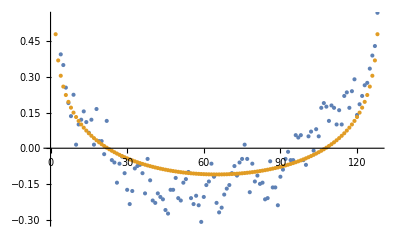

```mathematica
ListPlot[{corr2, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

```mathematica
n = 128;
corr = {0.71,0.41,0.31,0.22,0.27,0.12,0.18,0.16,0.1,0.16,0.15,0.2,0.04,0.09,0.11,-0.03,0.06,-0.03,-0.06,0.04,0.08,0.03,0.08,0,-0.1,-0.1,-0.05,-0.09,-0.08,-0.12,-0.1,-0.05,0,-0.2,-0.2,-0.16,-0.08,-0.23,-0.05,-0.06,-0.11,-0.04,-0.24,-0.17,-0.09,-0.04,-0.15,-0.15,-0.1,-0.12,-0.22,-0.13,-0.08,-0.16,-0.07,-0.02,-0.18,-0.05,0.01,0.08,-0.03,-0.08,-0.06,0.04,0,-0.05,-0.07,-0.12,-0.14,-0.25,-0.18,-0.21,-0.27,-0.2,-0.2,-0.27,-0.32,-0.26,-0.12,-0.08,-0.07,-0.1,-0.11,-0.2,-0.14,-0.12,-0.11,0.05,0.06,0.15,-0.01,-0.02,0.17,0.18,0.1,0.18,0.17,0.05,0.06,0.03,-0.05,-0.04,-0.04,0.07,0.03,-0.03,-0.06,0.06,0.07,0.05,0.06,0.14,0.1,0,0.13,0.24,0.1,0.21,0.04,0.08,0.03,0.11,0.13,0.09,0.24,0.25,0.34,0.42};
```

```mathematica
ListPlot[{corr2, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

-Graphics-

```mathematica
n=256;
corr3 = {0.86,0.57,0.44,0.28,0.28,0.24,0.08,0.2,0.18,0.28,0.38,0.31,0.42,0.32,0.25,0.28,0.16,0.17,0.17,0.19,0.13,0.15,0,0.04,0.11,0.16,0.09,0.05,0.08,-0.09,-0.06,0.04,-0.01,-0.18,0.04,0.17,0.09,0.14,0.07,0.01,-0.06,0.08,0.2,0.12,0.04,0.06,0.05,0.15,0.12,0.04,-0.05,-0.07,0.02,-0.03,0.02,-0.04,-0.01,0.07,0.11,-0.01,0.01,-0.14,-0.11,-0.17,-0.08,-0.13,-0.19,-0.14,-0.18,-0.11,-0.24,-0.12,-0.11,-0.03,-0.11,-0.04,0.02,-0.09,-0.08,-0.11,-0.06,-0.17,-0.06,-0.14,-0.06,-0.18,-0.18,-0.19,-0.07,-0.09,-0.02,-0.05,0.02,-0.03,-0.08,0.04,-0.13,-0.05,-0.11,0,-0.1,-0.04,-0.06,-0.04,-0.01,0.04,-0.17,-0.04,-0.1,0.04,-0.19,-0.08,-0.01,-0.19,-0.05,3.46945e-18,-8.67362e-18,-0.01,0.03,-0.17,-0.04,-0.07,1.04083e-17,-0.1,-0.06,-0.03,-0.07,-0.09,-0.15,-0.08,-0.09,-0.13,-1.04083e-17,0.01,-0.05,-0.05,-0.12,-0.15,-0.2,-0.13,-0.01,-0.14,-0.13,-0.13,-0.11,1.04083e-17,-0.04,0.11,0.04,0.06,-0.03,0.02,-3.46945e-18,-0.06,-0.01,0.04,-0.04,-0.06,-0.08,-0.04,-0.06,0.03,-0.09,0.07,-0.03,-0.04,0.03,2.77556e-17,-0.09,-0.08,-0.16,-0.14,-0.13,-0.19,-0.06,-0.02,-0.14,-0.09,-0.03,-0.06,-0.03,-0.02,0.08,-0.17,-0.06,0.03,-0.01,0.04,-0.05,-0.1,0,0.12,2.42861e-17,0.09,-0.1,-0.15,-0.12,-0.15,-0.06,-0.03,-0.17,-0.14,-0.16,-0.2,-0.15,-0.13,-0.03,-0.06,-0.06,-0.09,-0.03,-0.02,0.01,-0.15,-0.2,-0.04,-0.04,-0.26,-0.01,0.08,-0.02,-0.16,-0.11,-0.06,-0.06,-0.04,0.02,0.03,-0.02,-0.02,-0.04,-0.16,-0.07,0.09,-0.05,-0.02,-0.07,-0.06,0.15,0.11,0.11,0.12,0.18,0.33,0.18,0.16,0.17,0.25,0.25,0.2,0.2,0.22,0.29,0.3,0.34,0.44};
```

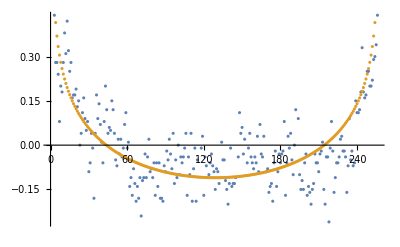

```mathematica
ListPlot[{corr3, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

### n = 128; correlations, k =3 fourier mode of height fluctuation

```mathematica
n=128;
corr4 = {0.4375,0.257812,0.154297,0.169922,0.146484,0.164062,0.111328,0.107422,-0.00195312,-0.0351562,0.0078125,0.00585938,0.00585938,-0.0332031,0.0214844,-0.0332031,-0.0136719,-0.0585938,-0.0449219,-0.0859375,-0.128906,-0.0546875,-0.113281,-0.132812,-0.09375,-0.0878906,-0.0410156,-0.0546875,-0.0429688,-0.00585938,-0.0703125,-0.0917969,-0.103516,-0.0527344,0.00195312,-0.0449219,-0.0625,-0.0703125,-0.0429688,-0.0761719,-0.0390625,0.0292969,0.0683594,0.105469,0.0292969,0.0332031,0.03125,0.0527344,0.0546875,0.134766,0.03125,-0.00585938,0.046875,0.0761719,0.0429688,0.0292969,0.0195312,0.0234375,-0.00585938,0.0390625,-0.0195312,0.0195312,0.03125,0.0175781,0,0.0742188,0.0351562,0,0.0898438,0.0996094,-0.0195312,0.0332031,-0.0273438,-0.0234375,-0.00976562,0.00195312,0.0703125,0.0234375,0.0253906,-0.015625,-0.0195312,-0.0351562,-0.0800781,0.0136719,-0.0332031,-0.0078125,-0.0429688,-0.0507812,-0.0683594,-0.0332031,-0.152344,-0.0878906,-0.109375,-0.0820312,-0.0722656,-0.111328,-0.0839844,-0.0800781,-0.0683594,-0.0292969,-0.078125,-0.0996094,-0.0761719,-0.0507812,0.0527344,0.0078125,-0.0820312,-0.015625,-0.0527344,-0.0664062,-0.119141,-0.125,-0.111328,-0.0800781,-0.0800781,-0.0429688,-0.0292969,0.0195312,0.0195312,0.0566406,0.0878906,0.0917969,0.0957031,0.140625,0.125,0.132812,0.169922,0.240234};
fourierevery64 = {0.0241305+I*(-0.0285452),-0.0953999+I*(0.0338531),0.264583+I*(0.283174),-0.0667152+I*(-0.521301),0.100487+I*(-0.158224),-0.199446+I*(0.258465),0.26475+I*(-0.423034),-0.0907601+I*(-0.760494),-1.2773+I*(-1.01226),0.46572+I*(0.0548084),-1.3017+I*(-0.563369),-0.393829+I*(-0.13399),0.0284996+I*(-0.0278862),0.541768+I*(0.343762),0.640817+I*(0.12418),1.10936+I*(-0.13681),1.85648+I*(-0.215155),-0.0468352+I*(-0.0660731),-0.817042+I*(-0.974551),0.350401+I*(-0.373755),-2.19342+I*(0.776133),-0.432504+I*(-0.601925),0.647137+I*(-1.15298),0.321009+I*(0.00149358),0.372855+I*(-0.42076),-0.216465+I*(0.273988),-0.14134+I*(0.12216),-0.0609338+I*(0.101617),4.03636+I*(3.28009),1.89723+I*(0.98254),0.687633+I*(0.333371),0.714806+I*(-0.928719),-0.998179+I*(-0.744289),0.186099+I*(0.366399),-0.441925+I*(-0.716175),0.869565+I*(0.844854),1.03932+I*(-0.3435),1.77021+I*(1.94188),0.948384+I*(0.821232),1.03021+I*(0.881388),0.4716+I*(0.413858),0.185221+I*(0.326386),1.15744+I*(-0.535417),0.484459+I*(-0.0369093),0.174517+I*(0.861219),0.821918+I*(-0.438357),-2.06792+I*(-0.509413),-0.65791+I*(-0.30125),0.698151+I*(0.774725),0.167927+I*(0.321556),0.0902979+I*(0.990416),-0.813554+I*(1.31424),-0.287526+I*(0.658301),1.57444+I*(0.839985),-0.248002+I*(0.229524),-0.453098+I*(-0.00291263),-0.600154+I*(-0.614602),-0.164154+I*(-0.220829),0.139781+I*(-0.394964),0.323937+I*(-0.92704),0.183645+I*(-0.036979),0.368525+I*(2.26643),1.03655+I*(0.396528),0.114458+I*(0.228505),0.649717+I*(0.150035),0.690982+I*(-0.409851),1.19591+I*(-0.744063),0.429361+I*(-0.386723),-0.209312+I*(0.739868),-0.00159314+I*(0.258214),0.824586+I*(0.545711),0.698478+I*(-0.153115),0.387224+I*(-0.141509),0.363698+I*(-0.0722399),-0.310206+I*(0.412417),1.79224+I*(-1.4399),1.51133+I*(0.389152),1.68764+I*(1.98829),1.41753+I*(-0.241551),1.58903+I*(-0.44721),1.62815+I*(-0.847385),0.710302+I*(-0.216612),0.188754+I*(-0.693448),0.0421096+I*(-0.213519),0.392648+I*(-1.1434),-0.229092+I*(1.05954),0.399653+I*(0.0217132),-2.26284+I*(2.55896),-1.59689+I*(1.02796),-0.466142+I*(0.940946),1.96008+I*(0.587877),2.44129+I*(2.48254),0.99685+I*(0.0622991),0.594505+I*(0.384662),-0.593416+I*(0.296212),-0.469995+I*(2.75828),0.177548+I*(2.26695),0.259258+I*(0.329796),-0.483295+I*(-0.376184),-1.1877+I*(-0.749909),-0.503892+I*(0.444248),-0.59392+I*(-0.0107988),-0.771038+I*(0.153975),-0.328031+I*(0.0416288),-0.757435+I*(1.12582),-0.282586+I*(0.44304),-0.519521+I*(0.057191),0.17858+I*(0.234887),-1.01486+I*(-1.13583),0.316252+I*(0.558825),-0.0757668+I*(0.569171),-0.242924+I*(-0.546176),0.820891+I*(0.305412),0.908277+I*(0.506272),0.167883+I*(2.42145),-0.591597+I*(1.28196),-0.973251+I*(-0.548921),0.314755+I*(-0.435455),-0.0805987+I*(0.614641),-0.267043+I*(-0.276317),0.181842+I*(-0.569678),-0.389778+I*(-1.03833),0.217629+I*(-1.79747),0.394486+I*(-1.08831),0.560963+I*(-1.10931),0.283984+I*(-0.318128),0.041625+I*(0.714501),1.37789+I*(-0.475486)};
martevery64 = {0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(0),0+I*(-0.000181307),0+I*(-0.000229702),0+I*(-0.000314881),0+I*(-0.000158413),0+I*(-0.000272943),0+I*(-0.000377954),-0.000126934+I*(-0.000396154),-0.000326445+I*(0.000403546),-0.000162245+I*(0.000336222),0+I*(0.000169739),-0.000220309+I*(0),-0.000157444+I*(0.00015484),0+I*(0.00097895),0+I*(0.00173267),-0.000319139+I*(0.00295353),-0.00109065+I*(0.00320645),-0.00175263+I*(0.000858667),-0.000857341+I*(-0.000788721),-0.00261177+I*(0.000943402),0.000231467+I*(0.00256249),0.000668921+I*(0.00395382),-0.00123268+I*(0.00283275),-0.000580635+I*(0.00415509),0.000895508+I*(0.00600645),0.00259963+I*(-0.000482905),0.00301895+I*(-0.00116827),0.00677614+I*(0.00339867),0.00182451+I*(0.00439103),-0.00217614+I*(0.00164809),0.00137718+I*(-0.000849694),0.0017636+I*(0.00771382),0.000947884+I*(0.00993352),0.0222893+I*(0.0241242),0.0194725+I*(0.026116),0.0127516+I*(0.024065),0.020568+I*(0.0603674),0.00946807+I*(0.0550894),-0.000866879+I*(0.0673368),0.0674102+I*(0.0280368),0.0174482+I*(0.03766),0.0305282+I*(0.0738848),0.0394138+I*(0.0919588),-0.0642463+I*(0.13004),0.0209599+I*(0.179821)};
```

### Analysis of corr4 fourierevery64

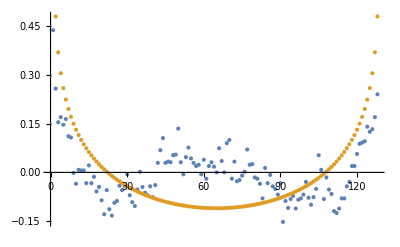

```mathematica
ListPlot[{corr4, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

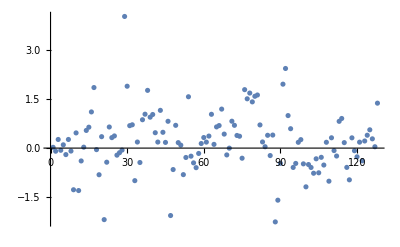

```mathematica
ListPlot[{Re[fourierevery64]} ]
```

### n = 512; correlations, k =3 fourier mode of height fluctuation

```mathematica
corr5 = {0.501953,0.308594,0.252441,0.183105,0.185059,0.197266,0.186523,0.171875,0.143066,0.142578,0.0961914,0.0668945,0.0708008,0.0722656,0.0283203,0.0415039,0.0415039,-0.0170898,0.03125,0.00537109,-0.0102539,0.0249023,-0.027832,-0.015625,-0.03125,-0.012207,0.00195312,0.0302734,0.0161133,0.0527344,0.0332031,0.00537109,0.00146484,-0.0209961,0.00292969,-0.00585938,-0.0366211,-0.0776367,-0.019043,-0.0449219,-0.0405273,-0.0317383,-0.0195312,-0.00976562,-0.0229492,-0.0415039,-0.015625,-0.0405273,-0.0419922,-0.0488281,-0.0922852,-0.065918,-0.0688477,-0.0234375,-0.0375977,-0.0371094,-0.0556641,-0.043457,0.00537109,0.0205078,0.0288086,0.0141602,0.0869141,0.0761719,0.0229492,0.0668945,0.0439453,-0.00634766,0.0371094,0.0356445,-0.00292969,0.00732422,-0.019043,-0.0141602,0.027832,0.00634766,-0.0166016,-0.0161133,-0.0341797,-0.0332031,0.00341797,0.0102539,-0.019043,-0.0439453,-0.0214844,-0.034668,0.0395508,-0.00195312,-0.0136719,0.00195312,0.0424805,0.0454102,0.0161133,0.0478516,0.0556641,0.0527344,0.0429688,0.0322266,0.00292969,-0.00244141,-0.0078125,0.0253906,0.0170898,-0.0078125,-0.00537109,-0.019043,-0.0532227,-0.0366211,-0.00585938,-0.0249023,-0.0131836,-0.043457,-0.0195312,0.0078125,-0.0327148,0.0297852,0.0600586,0.043457,0.059082,0.0634766,0.0224609,0.0483398,0.0493164,0.0820312,0.0693359,0.0571289,0.0366211,0.0693359,0.0639648,0.0629883,0.0610352,0.0410156,0.0200195,0.012207,0.0419922,-0.00195312,0.0473633,0.0131836,0.0297852,0.00634766,0.0263672,0.0610352,0.03125,0.0512695,0.0512695,0.0419922,0.0576172,0.0673828,0.0649414,0.101562,0.126953,0.108887,0.115234,0.133789,0.0634766,0.0537109,0.0727539,0.0161133,0.0390625,0.0576172,0.0302734,0.0224609,0.0458984,0.0625,0.0585938,0.0610352,0.034668,-0.0185547,-0.0136719,0.0268555,0.00634766,0.00830078,0.00195312,0.0200195,0.0429688,-0.0263672,-0.0415039,-0.00390625,0.00927734,0.0258789,0.0478516,0.0366211,0.0366211,0.0258789,-0.0239258,0.00634766,-0.0683594,-0.0322266,-0.00390625,-0.050293,-0.0322266,-0.0239258,-0.0170898,-0.0498047,0.00244141,-0.034668,-0.0424805,-0.0566406,-0.0654297,-0.0688477,-0.0825195,-0.0683594,-0.0766602,-0.0415039,-0.0341797,-0.0605469,-0.0620117,-0.0756836,-0.0717773,-0.0229492,-0.0117188,-0.03125,-0.0180664,-0.0161133,0.0170898,-0.00439453,0.019043,-0.0244141,0.0107422,0.0078125,-0.00537109,-0.0654297,-0.0185547,-0.0566406,-0.0673828,-0.0512695,-0.0429688,-0.0795898,-0.065918,-0.0957031,-0.146484,-0.131348,-0.126465,-0.103027,-0.0966797,-0.103516,-0.0385742,-0.0810547,-0.140625,-0.0844727,-0.103027,-0.0537109,-0.0405273,-0.0737305,-0.0566406,-0.0361328,-0.0541992,-0.0283203,-0.00927734,-0.0195312,-0.0112305,-0.0449219,-0.0366211,-0.0361328,0.0234375,-0.046875,-0.0473633,-0.0449219,-0.0141602,-0.0283203,-0.059082,-0.0263672,-0.046875,-0.0195312,-0.0688477,-0.0610352,-0.0732422,-0.0844727,-0.0419922,-0.0415039,-0.059082,-0.0532227,-0.0405273,-0.0756836,-0.03125,-0.0229492,-0.0307617,-0.0527344,-0.0302734,-0.0419922,-0.0566406,-0.114258,-0.106445,-0.11377,-0.108887,-0.103027,-0.0898438,-0.0795898,-0.101074,-0.0874023,-0.0893555,-0.0288086,0.00585938,-0.0195312,-0.00537109,-0.0141602,0.00195312,0.00244141,-0.0078125,-0.0463867,-0.0493164,-0.0268555,-0.0292969,-0.0307617,-0.0136719,-0.0112305,-0.00488281,-0.0126953,-0.0146484,0.00292969,0.0141602,0.00634766,-0.0234375,-0.0141602,0.0102539,-0.0146484,-0.0117188,-0.034668,-0.0361328,-0.0629883,-0.0473633,-0.0541992,-0.019043,0.0224609,0.0400391,0.0473633,0.000488281,-0.0336914,-0.0151367,-0.0273438,0.00537109,0.0175781,0.012207,-0.0224609,0.012207,0.0273438,0.0473633,0.00683594,0.00488281,-0.0205078,-0.00341797,-0.00244141,-0.0297852,-0.0249023,-0.0322266,-0.0756836,-0.0761719,-0.0512695,-0.0229492,-0.0551758,-0.0737305,-0.0410156,-0.0302734,-0.0327148,-0.046875,-0.0341797,-0.0458984,-0.0415039,-0.0146484,-0.0380859,-0.0390625,-0.00292969,-0.0444336,-0.0507812,-0.0322266,-0.0620117,-0.00683594,-0.0410156,-0.0820312,-0.0727539,-0.0786133,-0.0561523,-0.0644531,-0.00732422,-0.0449219,-0.0219727,-0.0439453,-0.0351562,-0.0297852,-0.0244141,-0.00927734,-0.0288086,-0.0424805,-0.0439453,-0.0522461,-0.0488281,-0.0161133,-0.034668,-0.0322266,0.0146484,-0.0234375,-0.046875,-0.0375977,-0.0400391,-0.0341797,-0.0444336,-0.0234375,-0.00927734,-0.0219727,-0.0356445,-0.0756836,-0.0771484,-0.074707,-0.0991211,-0.0942383,-0.0942383,-0.110352,-0.106934,-0.0888672,-0.0693359,-0.0581055,-0.0478516,-0.0737305,-0.123535,-0.0854492,-0.0703125,-0.043457,-0.0317383,-0.0395508,-0.0454102,-0.00976562,-0.0322266,0.012207,0.0263672,-0.00683594,-0.0268555,0.00488281,0.0283203,0.0166016,0.0385742,0.0219727,-0.0214844,0.00732422,-0.0800781,-0.0341797,0.0161133,-0.034668,-0.00390625,0.00830078,0.0112305,-0.00146484,0.0166016,0.0283203,0.059082,-0.000976562,0.0615234,0.0263672,0.0756836,0.0415039,0.0546875,0.0532227,0.0742188,0.0673828,0.0488281,0.0288086,0.00830078,0.0366211,0.0249023,0.0517578,0.0585938,0.0117188,0.0463867,0.0249023,0.0239258,0.00683594,0.0307617,0.0405273,0.0332031,0.00830078,0.0307617,0.0478516,0.0566406,0.027832,0.012207,0.0585938,0.0224609,0.0229492,0.0366211,0.0317383,0.0507812,0.0820312,0.0615234,0.0419922,0.0478516,0.000976562,0.0341797,0.0195312,0.0585938,0.0322266,0.0351562,0.0664062,0.106934,0.0878906,0.0678711,0.0942383,0.11084,0.115723,0.101074,0.130859,0.102051,0.0732422,0.0800781,0.127441,0.115723,0.145996,0.152832,0.186035,0.164062,0.190918,0.172363,0.251465,0.302246};
fourierevery256 = {-17.3205+I*(31.4811),-19.8746+I*(53.2788),-21.3702+I*(67.6921),-14.1608+I*(57.2649),-8.66385+I*(55.0861),-6.72707+I*(42.6257),-9.27511+I*(42.9504),-27.1204+I*(52.0765),-42.066+I*(52.3747),-28.3263+I*(38.5022),-16.9042+I*(66.3144),-23.0167+I*(46.2419),-7.54559+I*(62.6839),-30.4727+I*(59.6121),-16.7199+I*(73.6365),-4.21102+I*(68.4443),-8.22761+I*(48.2338),-18.2109+I*(29.8475),-11.56+I*(45.3601),-9.57329+I*(52.1966),-6.68282+I*(16.9189),9.00103+I*(20.4756),1.42365+I*(16.3584),-12.3877+I*(15.5916),0.927238+I*(14.004),-5.0059+I*(7.63056),19.1819+I*(-22.1679),4.79054+I*(-41.9931),11.5765+I*(-66.2727),17.496+I*(-64.7999),36.8659+I*(-81.4505),42.753+I*(-91.0082),46.4839+I*(-50.2045),52.9271+I*(-44.9368),51.7239+I*(-36.6606),63.7254+I*(-27.1387),52.7495+I*(-37.4823),49.3969+I*(-52.4985),30.2233+I*(-79.4597),27.318+I*(-85.095),23.1073+I*(-76.2024),9.03774+I*(-68.7063),1.67206+I*(-48.9899),-12.4823+I*(-41.2462),10.6524+I*(-43.1193),11.464+I*(-39.889),-0.489962+I*(-44.0462),14.1994+I*(-22.9874),28.6678+I*(-10.6875),51.0795+I*(-28.3167),43.8591+I*(-47.3994),49.5781+I*(-78.6799),45.0703+I*(-74.7265),34.2632+I*(-61.1828),71.814+I*(-41.1534),60.3858+I*(-45.6763),93.0572+I*(-38.9185),77.7678+I*(-38.697),41.541+I*(-60.8598),32.9228+I*(-61.3867),30.7271+I*(-81.1497),33.2326+I*(-73.0756),38.0748+I*(-71.6253),21.1825+I*(-99.3541),5.50767+I*(-83.1992),13.8298+I*(-100.524),9.34111+I*(-134.513),18.8993+I*(-109.062),39.0718+I*(-78.7006),25.5183+I*(-55.6983),17.9364+I*(-57.357),1.46722+I*(-28.7242),-19.9222+I*(-38.1972),-9.33725+I*(-29.9887),-8.09836+I*(-2.61366),-3.23904+I*(2.60208),-17.8627+I*(14.1856),-11.9973+I*(52.9362),-11.482+I*(37.1858),-24.0766+I*(34.5804),-11.9358+I*(48.303),-43.2106+I*(50.0334),-70.9019+I*(62.7222),-106.196+I*(56.1689),-131.057+I*(21.5603),-127.709+I*(14.8329),-105.49+I*(17.9336),-96.2029+I*(-14.2012),-97.229+I*(-16.709),-142.022+I*(-26.1954),-135.719+I*(-25.1997),-140.772+I*(-42.0124),-127.157+I*(-26.8161),-114.675+I*(-35.2402),-103.415+I*(-30.8169),-83.5821+I*(-27.5121),-110.261+I*(-17.4951),-95.7937+I*(-32.5545),-98.8101+I*(-59.2203),-106.719+I*(-67.33),-105.288+I*(-39.0197),-89.5595+I*(-40.0172),-71.13+I*(-43.1766),-75.3475+I*(0.148426),-81.9467+I*(-33.0447),-67.4568+I*(-33.4136),-71.7744+I*(-16.8149),-74.2202+I*(-2.03654),-50.871+I*(3.53939),-20.9212+I*(6.77907),-45.5389+I*(22.3479),-51.4509+I*(32.5346),-84.6119+I*(24.0463),-78.9691+I*(43.3726),-79.1816+I*(60.3702),-57.7927+I*(77.3717),-61.5099+I*(70.7703),-77.2128+I*(51.7674),-91.7647+I*(39.2836),-111.356+I*(22.6006),-106.98+I*(17.618),-127.638+I*(25.602),-105.407+I*(-0.775257),-78.435+I*(12.0434),-74.6182+I*(10.6459),-88.3819+I*(42.0802),-85.0437+I*(61.9505),-90.7261+I*(56.9044),-91.084+I*(71.204),-98.7863+I*(92.6134),-103.819+I*(56.1694),-107.158+I*(56.8635),-94.9617+I*(57.2516),-112.702+I*(16.6208),-109.346+I*(38.6006),-108.469+I*(48.7769),-87.9165+I*(70.4422),-80.9379+I*(44.5537),-95.4769+I*(44.5368),-107.355+I*(47.5355),-88.51+I*(61.1168),-93.4532+I*(61.2312),-79.5095+I*(55.0513),-58.3418+I*(43.5995),-66.1705+I*(36.7456),-74.104+I*(45.7763),-55.5663+I*(26.0251),-60.3806+I*(33.2775),-56.1272+I*(35.2572),-84.7122+I*(29.4662),-71.1807+I*(53.8906),-53.0006+I*(52.2701),-70.3806+I*(48.3138),-61.2668+I*(53.6245),-59.7436+I*(38.8754),-78.5698+I*(29.4417),-60.2337+I*(44.7122),-69.6681+I*(11.0598),-69.7953+I*(-6.53736),-62.0323+I*(-22.6395),-42.8469+I*(-26.2102),-26.9678+I*(-25.2184),-33.484+I*(-51.5633),-44.2063+I*(-73.8042),-43.3007+I*(-81.4408),-32.6659+I*(-56.1383),-54.3365+I*(-49.69),-51.7898+I*(-42.0385),-42.6945+I*(-26.6212),-44.9192+I*(-7.27785),-59.7083+I*(14.5803),-48.2486+I*(41.0509),-36.4498+I*(64.2852),-17.5788+I*(110.267),-19.4089+I*(109.651),-8.95573+I*(95.5418),-21.2797+I*(93.7232),-12.5689+I*(85.0054),-10.8538+I*(61.4536),-12.5261+I*(69.9848),-16.1885+I*(61.6254),-29.8065+I*(81.9217),-24.8334+I*(70.1941),-40.3318+I*(86.2016),-41.5803+I*(89.8937),-20.1616+I*(102.446),16.1884+I*(106.222),26.2199+I*(126.832),24.6918+I*(108.015),25.5569+I*(90.0741),0.738635+I*(83.2764),3.8337+I*(67.8632),-8.22185+I*(42.4441),-8.07541+I*(33.955),-41.5465+I*(48.3337),-25.6667+I*(52.0221),-51.7844+I*(63.4252),-66.0018+I*(65.6251),-59.1385+I*(48.4087),-28.7178+I*(30.3949),-25.891+I*(8.26153),-6.13461+I*(6.64074),-9.72826+I*(-28.2643),-8.96575+I*(-34.3902),-19.6478+I*(-40.5003),-27.4029+I*(-45.343),-28.7698+I*(-38.3279),-20.6315+I*(-45.246),-31.334+I*(-19.7301),-54.8642+I*(-2.69383),-54.5332+I*(-10.1865),-52.4481+I*(-18.955),-68.6147+I*(-19.0267),-41.811+I*(-39.6311),-36.2717+I*(-17.3313),-24.0916+I*(-38.558),-33.4657+I*(-32.598),-2.48826+I*(-20.7496),7.05556+I*(-28.5491),-6.7729+I*(-9.82795),30.0812+I*(-8.94718),36.9497+I*(2.94469),44.3245+I*(-29.1383),43.8041+I*(-27.927),52.6612+I*(-36.0781),67.2509+I*(-34.7347),66.581+I*(-16.2847),76.6475+I*(-3.38365),82.5047+I*(-1.34309),102.465+I*(-16.6287),114.877+I*(-30.7156),106.652+I*(-35.4712),105.038+I*(-46.7036),141.833+I*(-58.2784),130.659+I*(-52.1772),116.711+I*(-37.1901),113.968+I*(-66.3754),121.495+I*(-44.2379),126.652+I*(-48.8369),111.49+I*(-85.3498),115.947+I*(-76.3752),106.425+I*(-78.7671),105.687+I*(-98.0236),114.891+I*(-83.5876),124.557+I*(-68.2029),120.252+I*(-57.9478),109.326+I*(-41.9385),106.143+I*(-72.8973),111.265+I*(-69.6125),89.3913+I*(-63.6743),81.0733+I*(-63.2842),82.9889+I*(-41.666),71.297+I*(-10.0802),35.7009+I*(7.08461),42.4097+I*(13.3369),5.62884+I*(12.2383),35.3453+I*(11.3529),49.8396+I*(-11.6485),68.3303+I*(-19.8173),73.7329+I*(-10.4043),73.8659+I*(-22.1632),71.4351+I*(-18.0691),68.7965+I*(-39.1037),47.6709+I*(-24.6029),66.2425+I*(-28.5978),65.8132+I*(25.2818),96.8959+I*(5.85749),92.8332+I*(1.38981),119.969+I*(12.8147),119.593+I*(0.586726),125.116+I*(2.31083),89.029+I*(-6.26483),73.5923+I*(-17.1211),72.6936+I*(-21.4244),75.9268+I*(-30.2861),69.6595+I*(-30.1059),72.8486+I*(-30.1162),78.1501+I*(-56.3799),75.2043+I*(-59.5339),56.7882+I*(-71.3947),52.5983+I*(-73.514),22.1277+I*(-61.6539),55.0371+I*(-58.6373),57.9294+I*(-58.5138),42.1007+I*(-51.15),35.421+I*(-53.3912),29.1037+I*(-54.9877),31.4515+I*(-59.5689),16.6322+I*(-29.8683),9.17758+I*(-58.6553),18.1266+I*(-50.6605),20.3851+I*(-66.8169),34.4806+I*(-53.6916),35.4109+I*(-62.6236),36.5441+I*(-81.144),14.2642+I*(-65.8185),35.9887+I*(-52.7925),22.9753+I*(-40.2563),21.6574+I*(-68.5704),32.6842+I*(-76.0636),19.265+I*(-93.6639),47.0321+I*(-74.244),24.7891+I*(-56.2587),44.4277+I*(-30.0919),24.6752+I*(-29.325),2.71354+I*(-11.7152),-12.6241+I*(-26.255),-10.8595+I*(-39.5185),-3.97677+I*(-39.2947),-5.64979+I*(-42.072),-1.65256+I*(-38.2604),-8.38342+I*(-4.89534),14.0118+I*(-23.8812),16.0639+I*(-36.3607),31.1523+I*(-60.9269),34.2528+I*(-69.2108),10.0451+I*(-64.0789),12.6304+I*(-51.4841),43.0682+I*(-46.0506),26.18+I*(-30.6287),23.185+I*(-16.879),27.1355+I*(-17.7565),33.0966+I*(-37.4874),16.0273+I*(-33.0782),15.5268+I*(-49.4844),46.0337+I*(-50.7603),53.3627+I*(-50.4618),47.3558+I*(-53.3116),38.9287+I*(-59.626),21.2506+I*(-50.9108),15.2674+I*(-45.6404),9.96818+I*(-44.8304),-5.12443+I*(-64.4427),-28.2167+I*(-64.5846),1.09959+I*(-60.0309),2.83991+I*(-61.9913),-5.27362+I*(-70.9653),-12.6923+I*(-79.521),-8.23411+I*(-89.4715),-9.67273+I*(-71.0303),-11.3368+I*(-97.5789),-3.78367+I*(-91.7679),-6.32833+I*(-42.8181),0.484265+I*(-89.0444),-5.30042+I*(-57.4986),6.21755+I*(-64.1246),17.9681+I*(-74.2897),28.7557+I*(-89.2545),48.8302+I*(-77.1467),85.2026+I*(-89.2958),73.0412+I*(-83.7402),85.7893+I*(-75.2866),100.593+I*(-49.4448),115.787+I*(-60.0058),115.594+I*(-67.4372),116.227+I*(-77.8711),88.1123+I*(-56.4008),107.304+I*(-81.1855),103.257+I*(-73.6492),111.915+I*(-69.9551),104.019+I*(-68.9535),92.6923+I*(-51.3657),87.3259+I*(-36.4159),58.909+I*(-37.3533),63.4636+I*(-69.8149),84.9554+I*(-84.4309),72.7494+I*(-52.8352),81.1652+I*(-57.6502),91.9137+I*(-46.9618),99.2684+I*(-60.0185),102.029+I*(-43.3026),78.5812+I*(-23.9502),109.726+I*(-11.4624),90.136+I*(7.08049),111.136+I*(14.306),99.7821+I*(-2.96228),77.2115+I*(-24.1823),81.8219+I*(-35.3776),69.6996+I*(-44.5892),73.5476+I*(-32.3746),69.4159+I*(-21.276),84.4633+I*(-9.20528),65.3424+I*(-3.69466),53.4853+I*(4.87815),29.3481+I*(-25.269),47.174+I*(-37.7174),49.562+I*(-72.7926),76.6224+I*(-72.4297),107.719+I*(-54.7829),93.5229+I*(-40.0475),86.2496+I*(-48.0388),73.6773+I*(-39.6301),71.7045+I*(-26.0472),72.0638+I*(-39.3798),56.0657+I*(-31.4366),48.353+I*(-11.9161),76.2792+I*(-11.4111),100.389+I*(-37.187),84.9074+I*(-38.1548),94.8556+I*(-36.7031),93.4033+I*(-62.7163),90.4283+I*(-27.9242),75.2903+I*(-65.9102),68.7172+I*(-61.95),36.5098+I*(-89.1318),24.4969+I*(-106.921),19.1838+I*(-107.782),23.7482+I*(-99.0393),-3.42556+I*(-82.869),-22.4025+I*(-98.0026),-28.6016+I*(-111.533),-54.7337+I*(-109.771),-65.358+I*(-126.02),-43.7538+I*(-110.829),-39.3563+I*(-112.324),-54.7908+I*(-103.508),-42.9817+I*(-102.9),-14.385+I*(-81.9818),2.24692+I*(-95.5144),-21.251+I*(-96.1715),-8.30384+I*(-121.011),-36.222+I*(-110.942),-34.1919+I*(-81.2112),-41.2427+I*(-66.2617),-34.3656+I*(-60.1202),-19.0579+I*(-59.7165),-28.99+I*(-24.6504),-6.96965+I*(-39.461),-28.7668+I*(-50.2815),-28.4709+I*(-34.81),-15.216+I*(-18.7942),-3.37119+I*(-7.76433),-2.6035+I*(7.38993),5.30997+I*(8.3446),13.7911+I*(-0.256838),23.0574+I*(-0.546468),29.9918+I*(-2.46291),34.3322+I*(19.515),17.949+I*(25.7541),23.3357+I*(27.2216),29.238+I*(20.9088),23.6515+I*(34.9972),-5.0246+I*(20.876),5.50641+I*(17.5993),32.6162+I*(22.313),8.46399+I*(21.9809),-10.1097+I*(-0.451696),-26.705+I*(14.9811),-30.9321+I*(3.26371),-42.2516+I*(-8.42522),-43.4526+I*(-5.63298),-40.0756+I*(-21.7746),0.648672+I*(-16.091),22.1769+I*(-14.5141),10.1443+I*(-9.30222),6.0026+I*(4.13909),17.3071+I*(-16.7108),33.0563+I*(-13.8795),45.9598+I*(6.37676),36.3176+I*(14.5218),32.2685+I*(26.3315),39.1119+I*(50.364),13.4101+I*(63.3829),2.81749+I*(76.8333),-14.8034+I*(86.0486),0.0799981+I*(73.2642),-3.39323+I*(46.7568),4.16256+I*(54.4338),12.3232+I*(42.3686),-12.8481+I*(46.9002),-0.956954+I*(40.474),14.1897+I*(54.0321),-6.45496+I*(67.4908),-16.5353+I*(68.5556),-39.3231+I*(53.1875),-53.2546+I*(36.9652),-43.6744+I*(16.0467),-27.6831+I*(18.042),-24.9301+I*(44.0766),-17.6858+I*(41.5427),-14.5522+I*(62.9538),-15.951+I*(42.4634),-2.69875+I*(33.0301),20.9084+I*(37.8832),10.9329+I*(46.3095),10.6063+I*(21.7005),-7.06488+I*(44.2165),14.093+I*(56.3624),1.87864+I*(54.1413),-11.0369+I*(61.7079),11.2034+I*(50.3335),4.90514+I*(54.599),-17.0384+I*(38.2853),-9.03765+I*(42.9761),-8.358+I*(0.407966),18.009+I*(-18.2377),34.2284+I*(-2.61488),45.253+I*(36.9461),41.1229+I*(-4.99835),39.3583+I*(-1.52448),42.6123+I*(9.66869),38.7718+I*(-7.75758),44.2846+I*(13.0613),54.1598+I*(1.90019),48.6968+I*(-5.13616),27.6851+I*(0.879589),49.7883+I*(10.3669),42.3668+I*(-28.5167),59.9345+I*(-42.9997),34.0427+I*(-62.4396),22.572+I*(-64.7902),14.6822+I*(-72.9784)};
```

### Analysis of corr4 fourierevery256

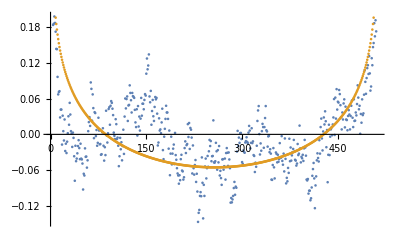

```mathematica
n=512;
ListPlot[{corr5, Table[-1/(8 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

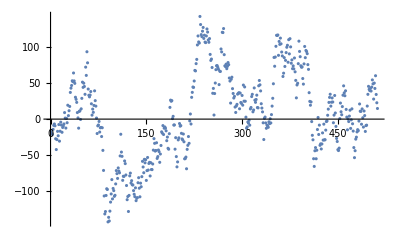

```mathematica
ListPlot[{Re[fourierevery256]} ]
```

```mathematica
fourierd = HistogramDistribution[Re[fourierevery256]/256.];
Moment[fourierd, 1]
Moment[fourierd, 2]
```

0.0246094

0.0557943

```mathematica
2 * f[3.]
```

0.0530474

### n = 512; 200 samples for y0 = 1/4; correlations, path of the martingale, k =3 fourier mode of height fluctuation

```mathematica
corr6 = {1.085,0.635,0.575,0.495,0.425,0.33,0.34,0.3,0.305,0.285,0.25,0.24,0.225,0.195,0.245,0.24,0.305,0.365,0.23,0.15,0.155,0.175,0.16,0.145,0.16,0.16,0.12,0.155,0.25,0.07,0.005,0.25,0.18,0.19,0.085,0.06,0.06,0.09,0.13,0.095,0.075,0.055,0.16,0.15,0.13,0.095,0.09,0.07,0.09,0.13,0.085,0.125,0.095,0.125,0.12,0.115,0.005,0.165,0.12,0.255,0.235,0.08,0.185,0.1,0.145,0.12,0.085,0.01,0.02,0.1,0.05,0.035,-0.01,0.055,-0.085,0.035,0.085,0.035,0.09,0.065,0.06,0.165,0.12,0.09,0.125,0.215,0.11,0.145,0.03,0.1,0.14,0.05,0.125,0.055,0.095,0.11,0.115,0.14,0.09,-0.03,0.12,0.11,0.11,0.05,0.09,0.09,0.045,0.075,0.065,0.085,0.09,0.12,0.05,0.025,0.035,0.115,0.03,-0.055,-0.055,0.055,0.05,0.115,-0.03,0.055,0,0.06,0.03,0.065,-0.035,-0.06,-0.14,-0.13,-0.025,-0.06,-0.025,-0.125,-0.02,-0.1,-0.12,-0.13,-0.035,-0.165,-0.04,0.04,-0.025,0.075,0.005,0.06,0.1,0.03,0.01,0.055,0,0.01,0.005,-0.045,0.07,-0.005,-0.11,-0.1,0.025,0,0.075,0.01,0.04,0.01,-0.06,0.015,-0.055,-0.03,-0.05,-0.035,0.015,0.025,-0.025,-0.105,-0.135,-0.06,-0.075,-0.12,-0.08,-0.135,-0.04,-0.005,-0.125,-0.23,-0.21,-0.15,-0.19,-0.115,-0.07,-0.18,-0.08,-0.04,-0.08,-0.025,-0.175,-0.23,-0.22,-0.215,-0.1,-0.04,-0.005,0.01,-0.015,-0.14,-0.04,-0.2,-0.1,-0.1,-0.105,-0.08,-0.115,-0.13,-0.095,-0.185,-0.2,-0.25,-0.17,-0.18,-0.115,-0.285,-0.105,-0.065,-0.11,-0.135,-0.115,-0.155,-0.12,-0.165,-0.115,-0.175,-0.17,-0.145,-0.08,-0.12,-0.105,-0.025,-0.035,-0.03,-0.08,-0.115,-0.015,-0.065,-0.08,-0.15,-0.175,-0.08,-0.17,-0.11,-0.12,-0.01,-0.07,-0.14,-0.05,-0.035,-0.135,-0.18,-0.13,-0.09,-0.09,-0.03,-0.14,-0.045,-0.105,-0.11,-0.16,-0.195,-0.195,-0.06,-0.18,-0.205,-0.145,-0.145,-0.13,-0.1,-0.155,-0.125,-0.015,0.055,-0.015,-0.06,0.005,-0.19,-0.08,-0.145,-0.155,-0.135,-0.135,-0.115,-0.055,-0.02,-0.13,-0.26,-0.195,-0.085,-0.12,-0.085,-0.115,-0.13,-0.055,-0.025,-0.16,-0.13,-0.1,-0.21,-0.085,-0.09,-0.005,-0.085,-0.1,-0.12,-0.145,-0.15,-0.155,-0.285,-0.305,-0.16,-0.22,-0.125,-0.12,-0.125,-0.185,-0.165,-0.185,-0.115,-0.035,-0.19,-0.24,-0.255,-0.1,-0.16,-0.15,-0.145,-0.115,-0.185,-0.16,-0.13,-0.1,-0.11,-0.22,-0.07,-0.05,-0.07,-0.09,-0.055,-0.085,-0.215,-0.23,-0.08,-0.15,-0.115,-0.06,-0.115,-0.175,-0.17,-0.215,-0.19,-0.1,-0.12,-0.18,-0.235,-0.205,-0.24,-0.315,-0.265,-0.18,-0.205,-0.105,-0.1,-0.19,-0.125,-0.135,-0.1,-0.115,-0.115,-0.05,-0.08,-0.125,-0.165,-0.07,-0.035,-0.045,-0.06,-0.03,0,-0.12,0,-0.04,-0.1,-0.16,-0.045,-0.08,-0.055,0.145,0.055,0.02,-0.045,-0.055,-0.06,-0.04,0.03,0.025,-0.065,-0.015,-0.045,-0.12,-0.06,0.015,-0.025,-0.105,-0.145,-0.12,-0.135,-0.125,-0.12,-0.125,-0.085,-0.13,-0.09,-0.065,-0.06,-0.04,-0.05,-0.09,-0.035,0.01,-0.1,0.05,0.04,0.055,0.015,0.085,0.03,0.085,0.055,0.08,0.05,0.075,0.14,0.095,0.09,0.175,0.06,0.15,0.195,0.045,0.075,0.08,0.075,0.09,0.145,-0.005,-0.035,0.1,0.115,0.055,0.11,0.095,0.085,0.13,0.1,0.01,0.13,0.075,0.025,0.19,0.155,0.23,0.13,0.095,0.16,0.165,-0.025,0.12,0.12,0.085,0.205,0.3,0.145,0.16,0.205,0.155,0.21,0.195,0.08,0.09,0.135,0.09,0.065,0.165,0.195,0.15,0.045,0.14,0.12,0.19,0.13,0.155,0.26,0.115,0.25,0.355,0.215,0.25,0.285,0.395,0.365,0.615,0.475,0.555,0.655};
```

### Analysis of corr4 fourierevery256

```mathematica
f[k_] =1/(4 Pi k) (1 - Exp[-  Pi k] );
```

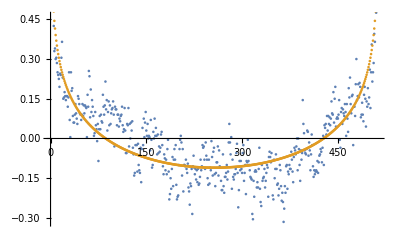

```mathematica
n=512;
ListPlot[{corr6, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

```mathematica
ListPlot[{Re[fourierevery256]} ]
```

-Graphics-

### n = 128; 100 samples for y0 = 1/4; correlations, path of the martingale, k =3 fourier mode of height fluctuation

```mathematica
corr61 = {0.71,0.41,0.31,0.22,0.27,0.12,0.18,0.16,0.1,0.16,0.15,0.2,0.04,0.09,0.11,-0.03,0.06,-0.03,-0.06,0.04,0.08,0.03,0.08,0,-0.1,-0.1,-0.05,-0.09,-0.08,-0.12,-0.1,-0.05,0,-0.2,-0.2,-0.16,-0.08,-0.23,-0.05,-0.06,-0.11,-0.04,-0.24,-0.17,-0.09,-0.04,-0.15,-0.15,-0.1,-0.12,-0.22,-0.13,-0.08,-0.16,-0.07,-0.02,-0.18,-0.05,0.01,0.08,-0.03,-0.08,-0.06,0.04,0,-0.05,-0.07,-0.12,-0.14,-0.25,-0.18,-0.21,-0.27,-0.2,-0.2,-0.27,-0.32,-0.26,-0.12,-0.08,-0.07,-0.1,-0.11,-0.2,-0.14,-0.12,-0.11,0.05,0.06,0.15,-0.01,-0.02,0.17,0.18,0.1,0.18,0.17,0.05,0.06,0.03,-0.05,-0.04,-0.04,0.07,0.03,-0.03,-0.06,0.06,0.07,0.05,0.06,0.14,0.1,0,0.13,0.24,0.1,0.21,0.04,0.08,0.03,0.11,0.13,0.09,0.24,0.25,0.34,0.42};
fourier61 = {-2.59945+I*(-21.104),-14.0299+I*(14.4915),-12.2468+I*(-1.5426),-8.40616+I*(8.35735),8.78255+I*(19.5326),8.68394+I*(-15.6529),3.19088+I*(1.52386),2.69417+I*(-17.3764),12.9374+I*(-18.4433),-8.33075+I*(4.44603),8.98428+I*(-9.5842),-1.96385+I*(9.07236),7.0859+I*(-17.4826),-14.2555+I*(-23.0225),7.00504+I*(39.6503),2.27227+I*(16.5955),32.8517+I*(9.65867),-2.80123+I*(32.6192),7.50301+I*(-16.4773),4.55742+I*(6.817),-2.09737+I*(-23.642),5.67415+I*(-9.9992),-28.1304+I*(-12.5291),31.8165+I*(-14.6571),4.74445+I*(-3.99092),-5.1246+I*(18.4946),-6.34577+I*(-48.5711),-20.029+I*(17.0014),-8.17838+I*(-3.30788),19.1048+I*(1.58301),10.7799+I*(3.81737),6.78674+I*(-9.00581),-12.8695+I*(9.77639),-26.7057+I*(12.8194),2.95492+I*(20.4518),5.89631+I*(-2.52674),-11.4307+I*(36.9995),-3.7368+I*(6.58288),18.9917+I*(24.8743),6.44789+I*(31.0991),-37.2022+I*(26.5699),19.1594+I*(7.8272),-5.18465+I*(-1.04873),12.0125+I*(-9.53631),-21.8801+I*(12.4374),-17.7704+I*(6.89534),10.3428+I*(14.542),-1.85449+I*(0.531387),-15.3687+I*(-14.0732),-4.71507+I*(20.0421),0.925088+I*(-2.2602),-13.4134+I*(3.41672),0.832442+I*(15.005),-25.2649+I*(-1.00032),-11.7137+I*(-10.4442),7.99078+I*(-7.0132),2.89629+I*(-10.5393),-7.58175+I*(-8.11409),6.28558+I*(-33.4659),-15.6826+I*(10.2877),-16.075+I*(-13.7894),-3.82108+I*(11.363),7.29324+I*(7.18248),11.9867+I*(-20.4888),-15.1542+I*(-4.86631),-23.6052+I*(14.5612),9.79692+I*(-0.566432),13.2787+I*(-7.06986),-5.60288+I*(-19.1146),28.7079+I*(-29.4724),-4.1926+I*(-7.34935),-2.91507+I*(8.6529),-8.06296+I*(-16.1266),-7.73851+I*(-51.1755),-7.21613+I*(1.61751),12.9326+I*(-8.83684),9.71838+I*(14.0096),-11.2227+I*(-18.9325),11.1201+I*(-13.5369),11.574+I*(0.448387),6.83741+I*(7.28497),-1.4644+I*(-2.77202),-14.3064+I*(-24.9051),-13.9459+I*(5.67629),-2.96399+I*(-9.9919),-7.07516+I*(-0.31004),-25.8887+I*(-21.8057),22.5171+I*(-2.53318),-4.84699+I*(22.2481),15.1491+I*(31.1187),-34.9008+I*(-18.3504),-9.45602+I*(-9.01991),-20.4876+I*(-22.1127),-5.01381+I*(7.83921),24.6955+I*(-22.0294),1.9558+I*(18.7573),-9.01151+I*(1.02467),-0.161151+I*(1.70817),-14.3552+I*(19.8587),23.4071+I*(-12.912)};
mart6 = {-0.0111487+I*(-0.148109),-0.103182+I*(0.0959592),-0.0894399+I*(-0.0117372),-0.0684356+I*(0.060955),0.0710704+I*(0.118445),0.0670066+I*(-0.0989732),0.0344043+I*(0.0222083),0.0166535+I*(-0.151238),0.11557+I*(-0.132534),-0.0451253+I*(0.0324476),0.0495582+I*(-0.0808163),-0.000207676+I*(0.0614406),0.0470442+I*(-0.138874),-0.089575+I*(-0.16875),0.0502309+I*(0.284751),0.0344622+I*(0.116435),0.243863+I*(0.0765045),-0.0150657+I*(0.232219),0.059962+I*(-0.12679),0.0258756+I*(0.0601826),-0.0210683+I*(-0.175757),0.0298677+I*(-0.0645567),-0.200269+I*(-0.0907662),0.224942+I*(-0.11291),0.050015+I*(-0.00707233),-0.022901+I*(0.136594),-0.0458369+I*(-0.344479),-0.141973+I*(0.123057),-0.0497028+I*(-0.0310087),0.128817+I*(0.010905),0.0867788+I*(0.0356464),0.0452672+I*(-0.0558111),-0.0867996+I*(0.085032),-0.182419+I*(0.104175),0.0287185+I*(0.162216),0.0405723+I*(-0.0211385),-0.0989459+I*(0.276555),-0.00891175+I*(0.0619996),0.139326+I*(0.181074),0.0323067+I*(0.236818),-0.259823+I*(0.194249),0.143072+I*(0.0495507),-0.0379508+I*(-0.00304998),0.0691492+I*(-0.0959854),-0.139032+I*(0.0756217),-0.128517+I*(0.0501201),0.0751845+I*(0.091709),-0.0304418+I*(0.013865),-0.11293+I*(-0.105088),-0.021287+I*(0.129754),-0.00297084+I*(-0.0174612),-0.0990831+I*(0.0343007),0.0095606+I*(0.100621),-0.182033+I*(-0.0106955),-0.0927263+I*(-0.103143),0.0522705+I*(-0.0558231),0.00517196+I*(-0.0777145),-0.0871317+I*(-0.0701185),0.0441758+I*(-0.254115),-0.112148+I*(0.084561),-0.11348+I*(-0.096521),-0.0311038+I*(0.0892085),0.0614055+I*(0.0579653),0.0844899+I*(-0.152276),-0.11716+I*(-0.0417041),-0.190924+I*(0.0958737),0.0794029+I*(-0.0346148),0.112805+I*(-0.0665948),-0.0214097+I*(-0.134079),0.201244+I*(-0.212473),-0.0398396+I*(-0.0462587),-0.0218503+I*(0.0372532),-0.0401591+I*(-0.1218),-0.0621166+I*(-0.366737),-0.0523667+I*(0.0105563),0.0929165+I*(-0.0591938),0.066137+I*(0.0969019),-0.0831336+I*(-0.127214),0.0930814+I*(-0.11203),0.0813344+I*(0.00638552),0.0182806+I*(0.0611846),-0.0173042+I*(-0.0257886),-0.0790116+I*(-0.177921),-0.0878565+I*(0.0531411),-0.0288192+I*(-0.0726824),-0.0563211+I*(0.0107472),-0.189612+I*(-0.158706),0.174113+I*(-0.00991236),-0.0312211+I*(0.155834),0.128862+I*(0.228239),-0.24212+I*(-0.141938),-0.0603894+I*(-0.0653723),-0.154865+I*(-0.180735),-0.0464256+I*(0.0688593),0.177886+I*(-0.162799),0.00152794+I*(0.140626),-0.0666991+I*(0.0115317),0.0135124+I*(0.0231095),-0.0942564+I*(0.151306),0.177581+I*(-0.0903757)};
```

### Analysis

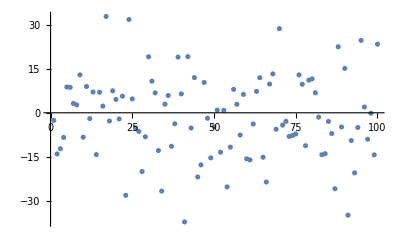

```mathematica
ListPlot[Re[fourier61]]
```

```mathematica
fourierd61 = HistogramDistribution[Re[fourier61]/128.];
Moment[fourierd61, 1]
Moment[fourierd61, 2]
```

-0.016

0.0135333

```mathematica
f[3.]/2
```

0.0132618

```mathematica
mart6d = HistogramDistribution[Re[mart6]];
Moment[mart6d, 1]
Moment[mart6d, 2]
```

-0.009

0.0113333

### n = 512; 100 samples for y0 = 1/4; correlations, path of the martingale, k =2 fourier mode of height fluctuation

```mathematica
corr7 = {1.27,0.71,0.7,0.68,0.68,0.65,0.46,0.49,0.63,0.37,0.42,0.44,0.43,0.39,0.31,0.42,0.47,0.35,0.42,0.23,0.33,0.38,0.4,0.32,0.45,0.44,0.19,0.22,0.2,0.18,0.01,0.31,0.16,0.22,0.14,0.13,0.18,0.19,0.27,0.1,0.18,0.19,0.27,0.11,0.1,-0.06,0.02,-0.15,-0.1,-0.21,0.02,-0.04,-0.05,-0.14,0.01,-0.03,-0.04,0.03,0.06,0.02,-0.02,0.11,-0.03,0.01,0.12,0.05,0.03,-0.04,-0.12,0.04,0.12,0.09,0.19,0.21,0.23,0.01,-0.02,0.01,0.03,0.17,-0.08,0.05,0.01,0.17,0.09,-0.02,-0.06,0,-0.05,-0.14,-0.05,0.07,-0.18,-0.05,0.03,-0.19,-0.12,0.11,0.02,0.01,0.12,0.14,0.11,0.06,0.17,0.12,-0.05,0.05,-0.04,-0.3,-0.3,-0.25,-0.26,-0.11,-0.03,-0.09,-0.1,-0.02,-0.1,0.06,-0.16,0,0.01,0.03,0.08,0.17,-0.03,0.18,0.03,0.17,0.22,0.21,0.14,0.19,0.18,0.21,0.24,0.16,0.3,0.01,0.21,0.08,-0.01,-0.07,-0.07,0.03,0.16,-0.09,0.11,0.08,0.13,0.21,0.09,0.13,0.01,-0.08,-0.12,0.03,0.01,0.15,-0.01,0.03,0.07,0.02,-0.02,-0.05,-0.06,-0.01,-0.21,-0.32,0,-0.11,0.05,-0.08,-0.03,-0.04,0.03,-0.17,0.04,-0.1,-0.17,-0.18,-0.16,-0.15,-0.27,-0.28,-0.19,-0.18,-0.3,-0.06,-0.05,-0.16,-0.2,-0.19,-0.14,-0.24,0.06,-0.29,-0.26,-0.1,-0.09,-0.12,0.02,-0.01,0.02,0.07,-0.04,-0.02,-0.08,0.02,-0.12,-0.09,0.03,-0.17,-0.13,-0.21,-0.19,-0.14,-0.09,-0.2,-0.1,0.1,0.21,0.15,0.07,0.14,0.05,-0.04,-0.09,-0.05,0,0.1,0,-0.18,-0.07,-0.04,-0.11,-0.18,-0.14,-0.11,-0.23,-0.13,-0.21,-0.06,0,-0.09,-0.33,-0.3,-0.18,-0.01,-0.13,-0.12,-0.14,-0.14,-0.33,-0.34,-0.32,-0.21,-0.34,-0.37,-0.43,-0.4,-0.37,-0.44,-0.31,-0.3,-0.43,-0.19,-0.3,-0.28,-0.33,-0.25,-0.23,-0.16,-0.04,-0.19,-0.29,-0.27,-0.18,-0.24,-0.25,-0.15,0.03,-0.21,-0.08,-0.15,-0.1,-0.12,-0.24,-0.16,-0.15,-0.1,0,0,-0.08,-0.05,-0.04,0.02,0.01,-0.08,-0.1,-0.07,0.06,-0.12,0,-0.05,-0.06,0.07,0.08,0.04,0.04,-0.1,-0.16,-0.23,0.01,-0.22,-0.25,-0.25,-0.14,-0.19,-0.16,-0.09,-0.23,-0.25,-0.21,-0.32,-0.16,-0.28,-0.15,-0.19,-0.33,-0.28,-0.29,-0.15,-0.22,-0.31,-0.25,-0.14,-0.24,-0.14,-0.11,-0.26,-0.15,-0.14,-0.17,-0.06,-0.04,-0.09,0.01,-0.06,-0.17,-0.1,-0.11,-0.1,-0.06,-0.04,-0.16,-0.23,-0.09,-0.27,-0.26,-0.42,-0.31,-0.22,-0.25,-0.33,-0.44,-0.23,-0.35,-0.41,-0.28,-0.29,-0.16,-0.13,-0.18,-0.19,0,-0.16,-0.2,0.07,-0.08,-0.12,-0.2,-0.14,-0.16,-0.21,-0.18,-0.22,-0.24,-0.34,-0.23,-0.1,-0.15,-0.1,-0.25,-0.26,-0.22,-0.37,-0.35,-0.19,-0.24,-0.08,-0.17,-0.17,-0.16,-0.13,-0.03,-0.03,-0.13,-0.13,-0.06,-0.13,0.02,0.04,0.01,0.09,0.09,0,-0.11,-0.1,-0.16,-0.2,-0.12,-0.14,-0.16,-0.15,-0.08,-0.2,0,-0.07,-0.14,-0.22,-0.1,-0.16,-0.19,0.07,-0.02,-0.02,0.01,0.01,-0.04,-0.07,0.05,0.02,-0.04,0.08,0.21,0.23,-0.01,0.05,0.37,0.2,0.17,0.21,0.18,0.16,0.09,0.13,0.32,0.09,0.16,0.08,0.11,0.06,0.16,0.17,0.39,0.25,0.25,0.2,0.1,0.18,0.02,0.21,0.2,0.04,0.14,0.31,0.24,0.3,0.36,0.09,0.14,0.31,0.3,0.38,0.27,0.44,0.32,0.33,0.46,0.45,0.38,0.44,0.42,0.39,0.34,0.42,0.53,0.5,0.38,0.45,0.44,0.49,0.61,0.62,0.64,0.49,0.42,0.57,0.57,0.56};
fourier7 = {70.782+I*(-26.6479),-81.269+I*(-33.9689),-19.7365+I*(-46.366),51.3581+I*(-152.265),155.183+I*(-0.0304595),-63.8349+I*(-55.257),-63.1468+I*(14.2945),-154.947+I*(-165.572),-26.7344+I*(4.77346),-122.272+I*(111.73),-60.2475+I*(-1.41037),45.9397+I*(-97.8557),-53.7578+I*(2.25776),-6.05611+I*(-28.284),24.829+I*(-68.8438),-11.9117+I*(106.192),23.7008+I*(54.4153),71.5912+I*(-39.4371),-56.121+I*(-95.221),23.0336+I*(50.0279),15.2566+I*(-100.886),88.2343+I*(83.0128),3.54942+I*(-116.164),-41.5281+I*(-2.98562),-113.764+I*(-19.4826),-51.6437+I*(-96.7329),-37.4733+I*(5.31716),-71.7211+I*(-47.248),-27.7332+I*(30.8853),-30.0212+I*(10.1544),-48.4675+I*(5.62839),-28.8472+I*(-113.538),4.94549+I*(-30.3062),56.0309+I*(-47.893),-67.6279+I*(-86.7154),32.2231+I*(-121.051),-20.0087+I*(16.945),92.6859+I*(-155.465),233.78+I*(52.9711),-131.144+I*(-124.497),64.5636+I*(-15.969),-142.297+I*(-6.83664),56.099+I*(139.97),-38.6273+I*(-91.8572),202.975+I*(-157.931),64.5929+I*(-28.0085),-117.573+I*(-33.6391),31.5645+I*(-13.1951),6.68858+I*(89.4109),0.432688+I*(-55.6894),-5.72565+I*(-70.7521),154.695+I*(-37.0877),47.2331+I*(-22.7554),47.3883+I*(-95.6653),70.3541+I*(-9.01796),8.66288+I*(-35.0182),-18.3455+I*(70.0009),59.3113+I*(-3.28506),24.772+I*(-31.0053),-86.8097+I*(-110.492),18.955+I*(84.8832),-171.393+I*(45.2154),-15.5619+I*(4.63326),11.4165+I*(46.9746),-56.3653+I*(-3.81642),133.67+I*(18.3574),-38.2825+I*(3.95719),92.6946+I*(-19.5001),-16.7977+I*(-19.7128),136.862+I*(-63.4742),55.0835+I*(-26.8933),7.02474+I*(-32.4049),-21.0041+I*(60.4054),114.062+I*(26.342),95.3235+I*(36.925),-87.3226+I*(-42.1688),8.33536+I*(55.5027),25.9835+I*(6.58206),-110.465+I*(20.7395),67.2028+I*(36.3907),-60.0656+I*(33.74),-113.28+I*(132.71),157.722+I*(-119.214),158.781+I*(-210.662),69.7365+I*(-99.5207),9.53233+I*(29.1918),-34.7642+I*(53.4921),19.8798+I*(78.9539),45.1224+I*(51.6776),-72.3828+I*(8.71727),65.352+I*(-50.9999),30.1013+I*(-158.947),65.5927+I*(49.3887),57.0732+I*(-70.8906),-52.719+I*(154.746),-30.8629+I*(-63.5722),-124.893+I*(-87.262),7.23093+I*(28.714),-54.1026+I*(-103.926),11.7566+I*(14.0976)};
mart7 = {0.137266+I*(-0.0568671),-0.164435+I*(-0.0709997),-0.0334841+I*(-0.0924226),0.103395+I*(-0.292901),0.299296+I*(0.00211396),-0.123959+I*(-0.106321),-0.117136+I*(0.0288328),-0.298565+I*(-0.319067),-0.0523351+I*(0.0113999),-0.236052+I*(0.213795),-0.121113+I*(0.000469513),0.0885577+I*(-0.185796),-0.104116+I*(0.0042801),-0.00898294+I*(-0.0603156),0.0478815+I*(-0.130616),-0.022534+I*(0.202805),0.0412961+I*(0.108258),0.134329+I*(-0.0767432),-0.106826+I*(-0.18323),0.0444629+I*(0.0973203),0.0288162+I*(-0.194894),0.173188+I*(0.160787),0.0080731+I*(-0.227782),-0.079482+I*(-0.00419404),-0.218344+I*(-0.0412652),-0.098189+I*(-0.186431),-0.0719616+I*(0.00976883),-0.137754+I*(-0.0946149),-0.055951+I*(0.0564603),-0.0604302+I*(0.0177525),-0.0988033+I*(0.0127381),-0.0585487+I*(-0.21428),0.0098921+I*(-0.0550831),0.108496+I*(-0.0930087),-0.130741+I*(-0.167929),0.0637064+I*(-0.235854),-0.0380888+I*(0.0312622),0.18053+I*(-0.299553),0.453915+I*(0.105452),-0.253986+I*(-0.239085),0.121563+I*(-0.0342702),-0.27328+I*(-0.0130558),0.106129+I*(0.277176),-0.075887+I*(-0.180792),0.391133+I*(-0.304675),0.124737+I*(-0.0563195),-0.226633+I*(-0.0690011),0.0688014+I*(-0.0235337),0.0109572+I*(0.17704),0.000220699+I*(-0.112408),-0.00588105+I*(-0.135956),0.302308+I*(-0.0756338),0.0913617+I*(-0.0436737),0.0894995+I*(-0.183486),0.132568+I*(-0.0171917),0.0187647+I*(-0.066232),-0.0379776+I*(0.134673),0.113535+I*(-0.00741728),0.0377465+I*(-0.0558975),-0.167199+I*(-0.214658),0.0344738+I*(0.162795),-0.333266+I*(0.0784345),-0.0314007+I*(0.00567281),0.0194103+I*(0.0885199),-0.100834+I*(-0.0047527),0.253162+I*(0.0297354),-0.070922+I*(0.00369231),0.185142+I*(-0.0369035),-0.0377108+I*(-0.0360021),0.264574+I*(-0.124093),0.109646+I*(-0.0504314),0.015131+I*(-0.0649092),-0.0451859+I*(0.119983),0.222828+I*(0.0444764),0.184154+I*(0.0699143),-0.169057+I*(-0.0809619),0.0221839+I*(0.110765),0.04906+I*(0.0117185),-0.216388+I*(0.0356167),0.130623+I*(0.0725703),-0.118391+I*(0.0674776),-0.217191+I*(0.255028),0.300258+I*(-0.228093),0.302148+I*(-0.407802),0.133868+I*(-0.189136),0.0180039+I*(0.0583533),-0.0682733+I*(0.10172),0.0362372+I*(0.149578),0.0826717+I*(0.102564),-0.141357+I*(0.0162046),0.130894+I*(-0.09549),0.0604542+I*(-0.306446),0.127716+I*(0.0864457),0.109945+I*(-0.141472),-0.100616+I*(0.298377),-0.0574695+I*(-0.125083),-0.242703+I*(-0.169052),0.0213384+I*(0.0525939),-0.102242+I*(-0.198069),0.0236523+I*(0.0291034)};
```

### Analysis

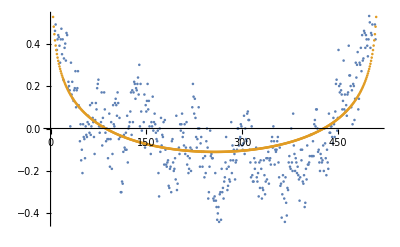

```mathematica
n=512;
ListPlot[{corr7, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

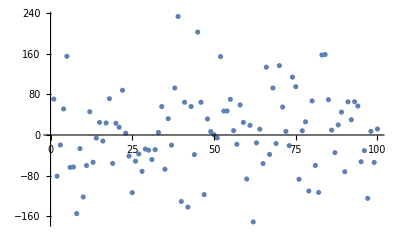

```mathematica
ListPlot[Re[fourier7]]
```

```mathematica
Moment[Re[fourier7]/512., 1]
Moment[Re[fourier7]/512., 2]
```

0.00854092

0.0233793

```mathematica
f[2.]/2
```

0.0198572

```mathematica
Moment[Re[mart7], 1]
Moment[Re[mart7], 2]
```

0.00838318

0.0228874

```mathematica
f[2.]/2
```

0.0198572

### n = 512; 100 samples for y0 = 1/4; correlations, path of the martingale, k =1 fourier mode of height fluctuation

```mathematica
corr8 = {1.04,0.65,0.57,0.52,0.41,0.34,0.37,0.39,0.34,0.41,0.33,0.33,0.29,0.32,0.41,0.33,0.32,0.29,0.32,0.23,0.25,0.32,0.25,0.29,0.37,0.4,0.44,0.32,0.33,0.3,0.25,0.33,0.35,0.16,0.12,0.21,0.12,0.28,0.33,0.36,0.25,0.08,0.16,0.09,0.24,0.25,0.24,0.22,0.12,0.21,0.12,0.17,0.03,0.26,0.19,0.21,0.27,0.1,0.02,0.17,0.06,-0.01,-0.04,-0.02,0.02,-0.09,0.11,0.18,0.12,0.11,0,0.01,-0.02,-0.03,0.18,0.14,0.07,0.06,0.18,0.14,0.07,0.1,0.01,-0.03,-0.03,0.05,0.21,0.09,0.13,0.09,0.09,0.08,0.18,0.07,0.09,-0.07,-0.06,0.06,-0.07,0.01,-0.05,0.03,-0.03,0.02,0.07,0,-0.11,0,0.12,0.08,-0.06,-0.05,-0.11,0.03,-0.03,0.07,0.12,0,-0.07,-0.1,-0.07,-0.09,0.03,-0.09,-0.01,0.04,0.12,0.11,-0.06,-0.03,0.02,0.09,0.04,0.18,-0.05,0.01,0.07,0.04,-0.23,-0.19,-0.1,-0.13,-0.15,-0.32,-0.18,-0.21,-0.12,-0.09,-0.13,-0.16,-0.19,-0.2,-0.21,-0.16,-0.16,-0.15,-0.04,-0.12,-0.03,-0.21,-0.18,-0.11,-0.14,-0.16,-0.29,-0.3,-0.22,-0.16,-0.18,-0.15,-0.07,-0.18,-0.2,-0.16,-0.21,-0.14,-0.15,-0.03,-0.05,-0.07,-0.1,-0.02,-0.13,-0.14,-0.12,-0.16,-0.21,-0.11,-0.06,-0.08,0.03,-0.08,-0.1,0.04,-0.25,-0.21,-0.08,-0.2,-0.1,-0.12,-0.15,-0.06,-0.19,-0.19,-0.04,-0.05,-0.18,-0.13,-0.06,-0.1,0,-0.12,-0.16,-0.13,-0.19,0.04,-0.16,-0.31,-0.21,-0.07,-0.05,-0.13,-0.03,-0.16,-0.15,-0.07,-0.26,-0.11,-0.12,-0.17,-0.06,-0.07,-0.11,-0.05,-0.15,0.02,-0.15,-0.15,-0.28,-0.33,-0.23,-0.2,-0.15,-0.28,-0.22,-0.18,-0.09,-0.04,0.03,-0.12,-0.05,-0.07,-0.17,-0.2,-0.15,-0.17,0,-0.24,-0.11,0.06,-0.11,0.11,0.04,-0.01,0.06,-0.08,-0.2,-0.22,-0.25,-0.09,-0.1,-0.16,-0.02,-0.12,-0.2,-0.14,-0.07,-0.24,-0.23,-0.08,-0.24,-0.32,-0.32,-0.31,-0.35,-0.28,-0.2,-0.16,-0.31,-0.27,-0.27,-0.21,-0.13,-0.04,-0.15,-0.15,-0.13,-0.1,-0.33,-0.24,-0.25,-0.19,-0.23,-0.29,-0.21,-0.2,-0.22,-0.16,-0.22,-0.22,-0.23,-0.17,-0.09,-0.29,-0.33,-0.33,-0.22,-0.13,-0.28,-0.19,-0.21,-0.19,-0.08,-0.21,-0.15,-0.1,-0.12,-0.11,-0.06,-0.13,-0.03,-0.08,-0.06,-0.16,-0.05,-0.09,-0.11,-0.12,-0.14,-0.03,-0.06,-0.09,-0.13,-0.14,-0.15,-0.17,-0.18,-0.03,-0.06,-0.14,-0.01,0.03,-0.02,-0.08,0,0.01,-0.09,-0.02,-0.07,-0.16,-0.17,-0.19,-0.17,-0.15,-0.3,-0.25,-0.21,-0.19,-0.17,-0.2,-0.03,0.07,-0.05,-0.1,0.01,-0.06,-0.05,-0.07,-0.18,-0.08,-0.16,-0.15,-0.18,-0.2,-0.1,0.03,-0.01,-0.02,-0.09,-0.07,-0.04,0.13,0.09,0.07,0.13,0.1,0.06,0.05,0.02,0.1,0.1,0.12,0.06,-0.02,-0.15,-0.02,0.09,0.08,0.08,0.03,-0.03,-0.03,-0.23,-0.06,-0.12,-0.04,-0.13,-0.11,-0.08,-0.18,-0.04,-0.12,-0.16,-0.08,-0.15,-0.1,-0.25,-0.27,-0.31,-0.08,-0.26,-0.13,-0.26,0.06,-0.01,0.02,0,-0.01,0.16,0.1,0.23,0.32,0.1,0.07,0.1,0.19,0.1,0.09,0.12,0.12,0.13,0.18,-0.08,0.04,0.08,0.02,0.06,0.15,0.05,0.06,0.15,0.15,0.07,0.37,0.12,0.26,0.23,0.31,0.19,0.12,0.13,0.13,0.08,0.2,0.26,0.24,0.16,0.14,0.24,0.15,0.17,0.24,0.23,0.18,0.17,0.17,0.12,0.11,0.24,0.24,0.14,0.2,0.32,0.21,0.21,0.24,0.35,0.35,0.38,0.38,0.44,0.3,0.41,0.48,0.45,0.6,0.47,0.46,0.64,0.54,0.64,0.75};
fourier8 = {91.1228+I*(111.915),-88.3143+I*(-15.0551),-124.34+I*(128.676),154.306+I*(79.0676),-50.6992+I*(-40.1287),14.8859+I*(-161.234),153.68+I*(175.58),30.9264+I*(-146.403),108.048+I*(317.162),-17.4862+I*(97.0529),147.367+I*(17.1429),-146.163+I*(-53.4855),-47.0718+I*(44.9221),-77.7505+I*(172.095),-189.353+I*(-26.4032),78.7147+I*(117.276),138.835+I*(68.9434),121.294+I*(49.3672),-2.61104+I*(-111.517),15.1176+I*(17.7464),12.3643+I*(-4.32581),-123.541+I*(-28.7141),-185.291+I*(-188.633),-56.5647+I*(184.565),35.7471+I*(-36.9041),19.2864+I*(61.1691),-68.2386+I*(-28.1779),121.143+I*(3.94872),-125.341+I*(-254.301),88.8479+I*(59.0222),9.76468+I*(-14.9906),-64.5917+I*(-119.488),-161.058+I*(41.1515),63.6764+I*(74.3829),172.129+I*(30.8867),109.593+I*(151.497),-20.6136+I*(157.869),99.3854+I*(1.93516),-72.7009+I*(-125.657),31.9403+I*(-4.92172),-167.723+I*(54.4389),-34.6125+I*(35.0402),187.926+I*(-55.6403),-182.151+I*(-118.483),55.5462+I*(-52.9523),-215.812+I*(-20.0719),76.6495+I*(-226.421),-157.437+I*(-288.478),-56.5997+I*(37.5896),86.4644+I*(224.779),27.6919+I*(-68.2862),-16.2968+I*(66.5373),109.854+I*(28.1699),-86.9458+I*(81.7357),139.611+I*(-129.266),31.6227+I*(33.2642),127.534+I*(38.7294),120.604+I*(30.6552),303.3+I*(30.6001),94.9359+I*(-91.3527),281.284+I*(-101.543),49.9727+I*(139.298),-152.543+I*(146.234),149.255+I*(-11.3497),128.469+I*(16.2179),-130.346+I*(-255.429),-103.866+I*(-1.87545),-11.4353+I*(11.3316),90.3695+I*(80.2499),67.6656+I*(-82.0771),-16.9298+I*(-67.1681),91.3239+I*(-148.979),122.072+I*(114.506),-85.4494+I*(-58.5487),125.119+I*(-125.005),-162.673+I*(41.482),-79.0894+I*(-113.888),81.4261+I*(-37.4693),-65.2794+I*(-136.573),-54.3481+I*(-414.57),73.4762+I*(150.11),-234.795+I*(-38.9503),-45.6747+I*(16.4626),-89.4144+I*(-217.235),122.046+I*(290.598),81.0908+I*(-128.448),-12.1143+I*(172.397),-0.173569+I*(30.0846),7.08525+I*(-137.337),-47.0715+I*(-89.2363),72.4796+I*(-29.6939),28.6913+I*(0.308054),236.55+I*(4.72792),-51.3617+I*(49.844),-192.768+I*(30.4143),-106.007+I*(128.316),203.225+I*(-3.66586),-98.0268+I*(-120.363),-71.5055+I*(138.143),-1.9256+I*(26.3217)};
mart8 = {0.176893+I*(0.221879),-0.166979+I*(-0.0283341),-0.240629+I*(0.249525),0.300609+I*(0.151012),-0.099579+I*(-0.0750164),0.0286053+I*(-0.309136),0.297346+I*(0.342707),0.0612063+I*(-0.281717),0.210144+I*(0.618169),-0.0378894+I*(0.192446),0.281751+I*(0.0370272),-0.280131+I*(-0.103353),-0.0860348+I*(0.0859884),-0.153289+I*(0.340239),-0.369079+I*(-0.0573976),0.154027+I*(0.230364),0.272688+I*(0.133394),0.231697+I*(0.102955),-0.00867159+I*(-0.215743),0.0282823+I*(0.0329788),0.0227203+I*(-0.00700511),-0.241623+I*(-0.0536125),-0.356878+I*(-0.36465),-0.113534+I*(0.358419),0.0712511+I*(-0.0742597),0.0356714+I*(0.120804),-0.12692+I*(-0.0572543),0.23393+I*(0.00684268),-0.236986+I*(-0.488029),0.170864+I*(0.112097),0.0126805+I*(-0.0271166),-0.120614+I*(-0.236717),-0.308577+I*(0.0841331),0.123331+I*(0.142959),0.336795+I*(0.0583717),0.210959+I*(0.293563),-0.0427401+I*(0.303121),0.189135+I*(0.0027415),-0.14312+I*(-0.241071),0.0590069+I*(-0.00827931),-0.327236+I*(0.106479),-0.0714096+I*(0.067481),0.361778+I*(-0.10582),-0.355903+I*(-0.223056),0.109405+I*(-0.10358),-0.420872+I*(-0.0435627),0.148291+I*(-0.443473),-0.307387+I*(-0.563904),-0.11015+I*(0.0715752),0.166929+I*(0.431829),0.0547488+I*(-0.128341),-0.0293239+I*(0.12941),0.216621+I*(0.052546),-0.170015+I*(0.158924),0.265487+I*(-0.24805),0.0622808+I*(0.0672135),0.247803+I*(0.0723262),0.235014+I*(0.0625613),0.583803+I*(0.0634201),0.186707+I*(-0.182322),0.546334+I*(-0.192525),0.0966568+I*(0.274618),-0.298066+I*(0.2855),0.290273+I*(-0.0231872),0.249937+I*(0.0371718),-0.247593+I*(-0.496216),-0.197717+I*(-0.00207098),-0.0223063+I*(0.0242879),0.173882+I*(0.156971),0.131688+I*(-0.164451),-0.0344988+I*(-0.130683),0.175801+I*(-0.288298),0.240993+I*(0.219364),-0.162096+I*(-0.118938),0.246822+I*(-0.242735),-0.318447+I*(0.0814324),-0.15249+I*(-0.217033),0.160578+I*(-0.0746356),-0.126524+I*(-0.269067),-0.109612+I*(-0.806328),0.142098+I*(0.290717),-0.456455+I*(-0.073765),-0.0889484+I*(0.0341737),-0.17158+I*(-0.418395),0.238716+I*(0.562197),0.154917+I*(-0.248426),-0.0230338+I*(0.335152),-0.00180309+I*(0.0587134),0.0158613+I*(-0.268976),-0.0923446+I*(-0.174281),0.141134+I*(-0.0573184),0.0550063+I*(0.00220645),0.460814+I*(0.0078241),-0.0993474+I*(0.0961105),-0.374277+I*(0.0588084),-0.206938+I*(0.24947),0.39382+I*(-0.00909199),-0.191272+I*(-0.233214),-0.131942+I*(0.268841),-0.00603325+I*(0.0518709)};
```

### Analysis

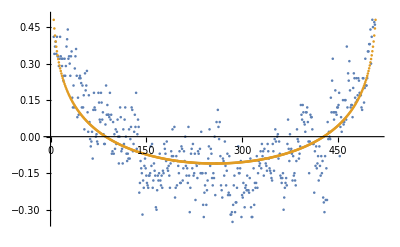

```mathematica
n=512;
ListPlot[{corr8, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

```mathematica
Moment[Re[fourier8]/512., 1]
Moment[Re[fourier8]/512., 2]
```

0.0163947

0.050168

```mathematica
f[2.]/2
```

0.0198572

```mathematica
Moment[Re[mart8], 1]
Moment[Re[mart8], 2]
```

0.016249

0.0494265

```mathematica
f[1.]/2
```

0.0380693

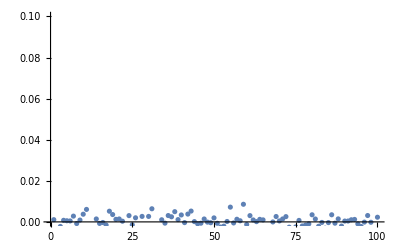

```mathematica
ListPlot[Re[fourier8]/512 - Re[mart8],PlotRange->{0,.1}]
```

```mathematica
Moment[Re[fourier8]/512 - Re[mart8], 2]
```

9.94941×10^-6

### n = 64; 100 samples for y0 = 1/4; correlations, path of the martingale, k =1 fourier mode of height fluctuation

```mathematica
corr9 = {0.87,0.35,0.14,0.27,0.12,0.11,0.06,0.06,-0.05,-0.02,-0.16,-0.12,-0.16,-0.06,-0.07,-0.02,-0.03,-0.1,-0.05,-0.06,-0.18,-0.19,-0.01,-0.11,-0.14,-0.13,0.02,-0.1,-0.05,-0.06,-0.13,0.04,-0.09,-0.1,-0.02,0.02,-0.09,-0.09,-0.06,-0.12,0,-0.05,-0.11,-0.06,-0.04,-0.12,-0.02,-0.04,-0.1,0.05,0.03,-0.08,-0.04,-0.04,0.06,-0.08,0.05,0.1,0.09,0.11,0.12,0.16,0.16,0.38};
fourier9 = {9.02757+I*(11.3945),-14.725+I*(18.9626),14.5697+I*(-3.62362),19.7669+I*(4.22669),-7.08181+I*(-24.1924),-19.1998+I*(5.01554),11.1478+I*(21.1612),3.884+I*(-8.15789),-16.3708+I*(-6.79465),25.2163+I*(17.9654),-21.9501+I*(14.7609),-0.0907814+I*(-3.855),12.1864+I*(2.09608),0.429543+I*(17.4686),10.8769+I*(-11.8588),-20.5519+I*(3.61264),-17.0319+I*(19.8479),-10.9282+I*(7.56903),6.77532+I*(26.894),23.5259+I*(0.186842),12.4311+I*(-4.29811),-4.89827+I*(0.827406),-9.23927+I*(-9.47654),21.0093+I*(7.29126),2.02169+I*(-21.5591),4.5557+I*(-10.5922),-0.949179+I*(-6.15267),-9.91542+I*(-10.8407),20.3264+I*(14.5313),-14.181+I*(16.9186),11.086+I*(18.8233),13.7686+I*(-21.8593),9.26784+I*(11.0081),-6.97711+I*(-3.17829),7.09539+I*(9.07223),-7.60274+I*(16.8529),23.3317+I*(-19.9936),-0.160195+I*(2.77206),14.7391+I*(-10.4847),23.8557+I*(-2.55344),7.21666+I*(-14.0841),-12.3156+I*(4.77425),16.0257+I*(-5.05399),-10.6166+I*(-16.2908),3.78588+I*(9.29194),1.78279+I*(-10.2453),7.10095+I*(-6.44395),7.36407+I*(10.6137),16.2924+I*(2.85788),4.46485+I*(6.20391),3.50895+I*(-4.26569),10.6247+I*(-11.1758),-13.3229+I*(-6.12281),-15.0547+I*(-17.0138),16.2199+I*(2.02862),-8.20972+I*(-5.23739),-2.01319+I*(-1.65036),10.4323+I*(-6.43853),9.34489+I*(4.84778),10.3052+I*(-10.5494),-6.8597+I*(-7.29744),25.5218+I*(-14.7089),29.4479+I*(23.6565),-12.0273+I*(3.66859),-5.73107+I*(-6.05455),2.22201+I*(-1.43702),20.5778+I*(19.2441),22.5285+I*(-11.7859),-5.0069+I*(-14.2359),-8.75968+I*(-3.88706),-6.74968+I*(-0.294154),-2.79606+I*(6.70469),0.701474+I*(-13.2594),3.81003+I*(-28.092),-0.954415+I*(-2.37129),-9.40316+I*(-0.213117),14.1235+I*(2.62047),1.27691+I*(-30.8611),-16.0565+I*(-1.52682),-2.22762+I*(6.45929),-5.37128+I*(-2.18952),21.6882+I*(6.65692),28.1314+I*(11.6361),9.8233+I*(-2.38684),8.21105+I*(31.7505),1.49118+I*(-0.372788),-4.1614+I*(-4.45501),3.41441+I*(25.1038),14.8771+I*(12.9809),-5.89924+I*(-9.94819),0.962709+I*(1.9975),16.3565+I*(-30.7488),-5.1257+I*(11.5481),-9.37478+I*(-32.4422),-13.5287+I*(13.8567),25.3443+I*(-3.3167),29.0171+I*(-5.98624),-13.8892+I*(-4.18967),18.7615+I*(-15.4433),19.0023+I*(-7.89467)};
mart9 = {0.128639+I*(0.163508),-0.200649+I*(0.300373),0.215825+I*(-0.0559507),0.284887+I*(0.0629562),-0.121614+I*(-0.346916),-0.282019+I*(0.0762918),0.158487+I*(0.328463),0.0492697+I*(-0.127551),-0.258299+I*(-0.100806),0.383139+I*(0.260253),-0.327698+I*(0.205991),0.00112366+I*(-0.0570434),0.189627+I*(0.0362041),0.00475523+I*(0.238768),0.151462+I*(-0.168758),-0.30016+I*(0.05508),-0.244377+I*(0.296563),-0.14467+I*(0.106456),0.111286+I*(0.412043),0.364952+I*(0.00170171),0.176563+I*(-0.041072),-0.0717557+I*(0.0131414),-0.140086+I*(-0.148664),0.297988+I*(0.101399),0.0182415+I*(-0.329403),0.0685592+I*(-0.160199),-0.0143546+I*(-0.0865853),-0.140729+I*(-0.150659),0.308335+I*(0.188587),-0.215705+I*(0.257227),0.159879+I*(0.274863),0.205867+I*(-0.323113),0.137253+I*(0.159384),-0.121265+I*(-0.0596886),0.0937501+I*(0.124589),-0.101362+I*(0.288429),0.346874+I*(-0.290829),-0.00667624+I*(0.0345367),0.195336+I*(-0.156101),0.372345+I*(-0.0309338),0.105651+I*(-0.202025),-0.155881+I*(0.0797124),0.270801+I*(-0.0775555),-0.162103+I*(-0.256511),0.054991+I*(0.136423),0.0279696+I*(-0.15731),0.106844+I*(-0.0915487),0.10858+I*(0.155474),0.231576+I*(0.0108976),0.0667456+I*(0.0990736),0.072206+I*(-0.0561377),0.168317+I*(-0.159391),-0.198206+I*(-0.0964537),-0.245998+I*(-0.24266),0.237229+I*(0.0497837),-0.128675+I*(-0.0562217),-0.0246987+I*(-0.0208796),0.14404+I*(-0.103854),0.130574+I*(0.0780791),0.150553+I*(-0.162476),-0.102807+I*(-0.107638),0.375021+I*(-0.233562),0.438609+I*(0.351915),-0.180497+I*(0.0578636),-0.0818281+I*(-0.0956351),0.0377209+I*(-0.0220634),0.301524+I*(0.29398),0.331882+I*(-0.178007),-0.0769045+I*(-0.216028),-0.128617+I*(-0.0509107),-0.096943+I*(-0.00604118),-0.0206935+I*(0.0798172),0.0120054+I*(-0.19626),0.0677345+I*(-0.410858),-0.01638+I*(-0.0367471),-0.141791+I*(-0.00386822),0.193497+I*(0.0325786),0.0158403+I*(-0.457233),-0.253474+I*(-0.00150448),-0.0355194+I*(0.103312),-0.0806055+I*(-0.0369782),0.326377+I*(0.123917),0.415181+I*(0.183406),0.146153+I*(-0.0281768),0.12049+I*(0.485406),0.0237547+I*(-0.000554242),-0.0641416+I*(-0.0539779),0.0541463+I*(0.371448),0.20151+I*(0.205812),-0.0836164+I*(-0.149294),0.0175517+I*(0.0217063),0.244584+I*(-0.456008),-0.0731493+I*(0.17087),-0.123818+I*(-0.494805),-0.200989+I*(0.204612),0.379922+I*(-0.0457442),0.427651+I*(-0.0913552),-0.22295+I*(-0.0811808),0.274419+I*(-0.22327),0.276021+I*(-0.128898)};
Dphi9 = {0.141056+I*(0.162415),-0.230079+I*(0.29629),0.227652+I*(-0.056619),0.308858+I*(0.066042),-0.125089+I*(-0.372027),-0.299997+I*(0.0783677),0.174185+I*(0.330644),0.0606874+I*(-0.127467),-0.255794+I*(-0.106166),0.394005+I*(0.280709),-0.342971+I*(0.230639),-0.00141846+I*(-0.0602343),0.190412+I*(0.0327513),0.00366332+I*(0.257622),0.165374+I*(-0.174245),-0.321123+I*(0.0564475),-0.266124+I*(0.310124),-0.156972+I*(0.110901),0.105864+I*(0.420219),0.367592+I*(0.00291941),0.1897+I*(-0.0522058),-0.0765355+I*(0.0129282),-0.144364+I*(-0.148071),0.316192+I*(0.104014),0.0270532+I*(-0.351812),0.0711828+I*(-0.165503),-0.0148309+I*(-0.0961354),-0.154928+I*(-0.153761),0.317599+I*(0.195802),-0.221578+I*(0.264354),0.173219+I*(0.294113),0.215135+I*(-0.341551),0.14481+I*(0.172002),-0.122797+I*(-0.0570264),0.0998169+I*(0.130705),-0.10888+I*(0.291029),0.364557+I*(-0.3124),-0.00250305+I*(0.0433135),0.215863+I*(-0.169804),0.384824+I*(-0.0299851),0.11276+I*(-0.220064),-0.164803+I*(0.0829786),0.266027+I*(-0.0789686),-0.174565+I*(-0.267536),0.0591544+I*(0.145187),0.0278561+I*(-0.160084),0.110952+I*(-0.100687),0.115064+I*(0.165839),0.244022+I*(0.0191922),0.0697634+I*(0.0969361),0.0701521+I*(-0.0636031),0.166012+I*(-0.174622),-0.20817+I*(-0.0956689),-0.242595+I*(-0.25206),0.253437+I*(0.0316972),-0.134256+I*(-0.0673987),-0.031456+I*(-0.0257869),0.163004+I*(-0.100602),0.146014+I*(0.0788096),0.161018+I*(-0.164835),-0.107183+I*(-0.114023),0.398778+I*(-0.229826),0.460124+I*(0.369633),-0.187927+I*(0.0573218),-0.089548+I*(-0.0946023),0.0347189+I*(-0.0224534),0.321528+I*(0.30069),0.352009+I*(-0.184154),-0.0782329+I*(-0.222436),-0.13687+I*(-0.0607353),-0.105464+I*(-0.00459615),-0.0195318+I*(0.0849359),0.0109605+I*(-0.207179),0.0725234+I*(-0.430257),-0.0149127+I*(-0.0370515),-0.146924+I*(-0.00332995),0.205354+I*(0.0378966),0.0199516+I*(-0.482205),-0.252414+I*(-0.00830681),-0.0348065+I*(0.100926),-0.0839262+I*(-0.0342113),0.343414+I*(0.118967),0.439553+I*(0.181814),0.153489+I*(-0.0372944),0.128298+I*(0.496102),0.0232996+I*(-0.00582482),-0.0760704+I*(-0.0585609),0.0533502+I*(0.392247),0.21683+I*(0.202827),-0.0921757+I*(-0.15544),0.0150423+I*(0.031211),0.25557+I*(-0.48045),-0.0800891+I*(0.180439),-0.131156+I*(-0.503861),-0.211387+I*(0.21651),0.396004+I*(-0.0518235),0.456441+I*(-0.10886),-0.226932+I*(-0.0775419),0.293149+I*(-0.241301),0.296911+I*(-0.123354)};
```

### Analysis

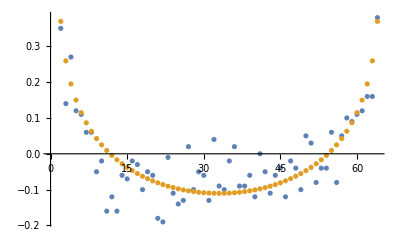

```mathematica
n=64;
ListPlot[{corr9, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

```mathematica
Moment[Re[fourier9]/n, 1]
Moment[Re[fourier9]/n, 2]
f[1.]/2
```

0.0570854

0.0442388

0.0380693

```mathematica
Moment[Re[mart9], 1]
Moment[Re[mart9], 2]
f[1.]/2
```

0.0539041

0.0399113

0.0380693

```mathematica
Moment[Re[Dphi9], 1]
Moment[Re[Dphi9], 2]
f[1.]/2
```

0.0569446

0.0441062

0.0380693

### n = 1024; 100 samples for y0 = 1/4; correlations, path of the martingale, k =1 fourier mode of height fluctuation

```mathematica
corr9 = {1.45,1.08,0.92,0.91,0.73,0.95,0.48,0.63,0.62,0.57,0.28,0.39,0.34,0.5,0.44,0.44,0.21,0.24,0.13,0.23,0.29,0.36,0.29,0.21,0.36,0.22,0.37,0.42,0.43,0.26,0.36,0.46,0.42,0.24,0.2,0.29,0.28,0.21,0.29,0.45,0.35,0.32,0.43,0.18,0.34,0.14,0.06,0.14,0.26,0.18,0.24,0.37,0.17,0.17,0.11,0.2,0.08,0.18,0.27,0.05,0.11,0.17,0.35,0.34,0.28,0.04,0.25,0.01,0.1,0.13,0.16,0.23,0.14,0.33,0.11,0.13,0.14,0.21,0.27,0.2,0.33,0.2,0.26,0.3,0.37,0.07,0.23,0.16,0.11,0.18,-0.15,0.06,0.06,0.05,-0.09,0.03,0.09,0.04,0.09,0.13,0.18,0.1,0,0.03,0.1,0.12,0.22,0.1,0.15,0.13,0.22,0.14,0.19,0.24,0.15,0.2,0.12,0.1,0.06,0.07,0.08,-0.08,-0.12,0.13,0.14,-0.02,-0.02,0.03,0.26,0.11,0.06,-0.01,-0.03,0.05,-0.05,-0.14,-0.19,0,0.09,0.06,0.05,0.25,0.04,-0.08,-0.09,0.02,-0.01,0.07,-0.04,0.16,0.13,-0.04,-0.05,0.06,-0.09,0.07,0.06,0.12,0.07,0.03,0.24,0.25,0.11,0,-0.07,-0.02,-0.03,-0.18,0.01,-0.01,0.04,0.17,0.2,0.02,-0.03,0.1,-0.1,0.06,0.03,0.16,-0.19,-0.1,-0.26,-0.2,-0.28,-0.25,-0.26,-0.09,-0.09,0,-0.06,-0.05,-0.04,0.14,0.06,-0.26,-0.13,-0.25,-0.19,0.05,-0.02,-0.03,0.11,-0.1,0,0.11,-0.07,-0.1,-0.04,-0.06,-0.01,0.08,-0.14,-0.08,-0.16,-0.18,-0.22,-0.06,-0.11,-0.01,-0.15,-0.12,-0.07,-0.19,-0.01,-0.18,-0.13,0.11,-0.01,-0.1,-0.18,-0.35,-0.21,-0.12,-0.2,-0.1,-0.18,-0.17,-0.17,-0.06,-0.01,-0.06,0.02,-0.11,-0.13,-0.21,-0.02,0.07,-0.01,0.05,0.01,-0.06,0.06,-0.1,-0.04,-0.02,0.07,-0.03,-0.04,-0.11,-0.29,-0.22,-0.16,-0.07,-0.12,-0.13,-0.02,0.08,0.04,-0.02,-0.02,0.03,-0.06,0.04,-0.22,0.05,0.03,0.12,0.13,0.08,-0.14,0.1,-0.11,-0.22,-0.36,-0.24,-0.01,-0.14,-0.05,-0.09,-0.16,-0.16,-0.13,-0.25,-0.17,-0.13,-0.05,0.01,0.02,0.04,-0.08,-0.16,-0.13,-0.01,0.01,0.01,-0.15,-0.03,0.17,-0.08,-0.04,0.03,-0.09,-0.36,-0.19,-0.05,-0.15,-0.2,-0.18,-0.14,-0.17,-0.08,-0.15,-0.31,-0.16,-0.16,-0.12,-0.21,-0.14,-0.27,-0.11,-0.21,-0.19,-0.21,-0.08,-0.14,0,-0.04,0.13,-0.07,-0.03,-0.12,-0.08,-0.1,-0.06,-0.27,-0.3,-0.21,-0.13,-0.09,-0.08,-0.16,-0.31,-0.08,-0.1,-0.25,-0.27,-0.16,-0.02,-0.02,-0.19,-0.13,-0.3,-0.14,-0.18,-0.14,-0.29,-0.16,-0.34,-0.31,-0.06,-0.18,-0.12,-0.08,-0.07,-0.08,-0.15,-0.12,-0.08,-0.17,-0.09,-0.02,-0.04,-0.05,-0.05,-0.15,-0.2,-0.06,-0.04,0.06,-0.07,0.13,0.03,-0.05,0.08,-0.05,-0.06,0.09,0.07,-0.17,-0.08,-0.08,-0.06,0.03,-0.08,0.1,0.05,-0.06,-0.1,0.07,0.01,-0.11,-0.07,-0.11,-0.12,-0.05,0.02,0.01,0.01,0.18,-0.1,-0.02,0.03,-0.12,-0.06,0.07,-0.22,-0.18,-0.27,-0.16,-0.18,-0.13,-0.1,-0.21,-0.23,-0.04,-0.18,0.02,-0.29,-0.19,-0.17,-0.12,-0.07,-0.12,-0.03,-0.01,-0.17,0.07,0.04,-0.05,-0.09,0.04,-0.24,-0.04,-0.06,0,-0.08,-0.06,-0.09,-0.06,-0.07,-0.14,-0.05,-0.08,-0.27,-0.16,-0.28,-0.31,-0.32,-0.24,-0.13,-0.31,-0.15,-0.13,-0.16,-0.21,-0.08,-0.15,-0.31,-0.15,-0.18,-0.19,-0.06,-0.07,-0.22,-0.06,-0.18,-0.22,-0.13,-0.03,-0.14,-0.07,-0.05,-0.03,-0.07,-0.1,-0.02,-0.15,-0.05,-0.08,0.03,-0.2,-0.04,-0.11,-0.15,0.03,-0.04,-0.15,-0.12,-0.13,-0.14,-0.23,0.06,-0.21,-0.25,-0.11,-0.41,-0.16,-0.04,-0.1,0.11,-0.18,-0.01,-0.17,-0.22,-0.21,-0.2,-0.04,-0.15,-0.18,-0.12,-0.12,-0.07,-0.04,-0.07,0.01,-0.15,-0.14,-0.15,-0.19,-0.18,-0.26,-0.31,-0.2,-0.12,-0.18,-0.26,-0.25,0.06,-0.13,-0.02,0.05,-0.16,-0.01,-0.06,0.02,-0.02,0,-0.26,-0.23,0.01,-0.11,-0.19,-0.21,-0.1,-0.11,-0.07,-0.05,-0.06,-0.15,-0.08,-0.27,-0.24,-0.34,-0.23,-0.26,-0.38,-0.17,-0.1,-0.23,-0.25,-0.3,-0.19,-0.13,-0.25,-0.26,-0.23,-0.31,-0.3,-0.34,-0.31,-0.24,-0.29,-0.42,-0.12,-0.19,-0.17,-0.2,-0.1,-0.18,-0.05,-0.14,-0.07,-0.09,-0.06,-0.15,-0.05,-0.23,-0.11,0.03,-0.1,-0.14,-0.21,-0.27,-0.23,-0.24,-0.29,-0.25,-0.26,-0.3,-0.2,-0.34,-0.34,-0.16,-0.09,-0.34,-0.27,-0.23,-0.19,-0.26,-0.19,-0.38,-0.25,-0.29,-0.4,-0.09,-0.07,-0.16,-0.06,-0.07,-0.19,-0.27,-0.1,-0.11,-0.17,-0.12,-0.18,-0.28,-0.13,-0.19,-0.31,-0.23,-0.3,-0.33,-0.36,-0.22,-0.26,-0.17,-0.37,-0.31,-0.2,-0.36,-0.26,-0.22,-0.31,-0.18,-0.28,-0.39,-0.29,-0.19,-0.06,-0.08,-0.24,-0.18,0.03,-0.26,-0.22,-0.14,-0.29,-0.08,-0.04,-0.15,-0.13,-0.12,-0.21,-0.11,-0.19,-0.19,-0.2,-0.05,-0.13,-0.29,-0.12,0.03,-0.01,0.01,-0.01,-0.09,-0.03,0.03,-0.02,-0.06,0.02,-0.1,-0.1,-0.1,-0.05,-0.04,-0.07,-0.18,-0.03,-0.02,-0.19,-0.12,-0.12,-0.05,-0.23,-0.04,-0.11,-0.17,0.03,-0.1,-0.29,-0.22,-0.23,-0.33,-0.24,-0.21,-0.1,-0.03,-0.1,-0.23,-0.16,-0.05,-0.07,-0.16,-0.04,-0.2,-0.07,-0.24,-0.27,-0.15,-0.21,-0.29,-0.16,-0.12,-0.27,-0.21,-0.21,-0.25,-0.04,-0.18,-0.09,-0.12,-0.07,-0.18,-0.26,-0.27,-0.27,-0.22,-0.22,-0.3,-0.24,-0.28,-0.14,-0.06,-0.17,-0.07,-0.07,-0.17,-0.05,-0.06,-0.18,-0.17,-0.2,-0.18,-0.13,-0.09,0.01,0.1,0.04,-0.01,0.03,0.05,-0.04,-0.04,0.09,-0.01,-0.03,-0.02,-0.03,0,-0.08,-0.03,-0.01,0.18,0.17,0.11,-0.03,0.11,0.13,-0.18,0.02,-0.03,-0.07,0.11,0.06,0.05,0.06,0.13,-0.01,-0.28,-0.17,0.04,0.09,0.09,0.07,0.03,0,0.02,0.15,0.18,0.01,-0.04,0.01,0.01,0.11,0.1,0.11,0.1,0.01,0.23,0.14,-0.06,0.25,0.16,0.07,-0.07,-0.04,-0.05,-0.04,-0.02,-0.04,0.15,0.19,-0.03,0.07,0.21,0.15,-0.06,0.07,-0.02,0.15,0.25,0.32,0.3,0.22,0.15,0.13,0.16,0.21,0.18,0.22,0.21,0.09,0.23,0.22,0.21,0.16,0.26,0.16,0.19,0.07,0.13,0.03,0.17,-0.02,0.08,0.22,0.18,0.24,0.29,0.16,0.07,0.25,0.12,0.09,0.06,0.13,0.1,-0.02,0.13,0.2,0.16,0.09,0.18,0.18,0.11,0.05,0.15,0.02,-0.02,0.02,0.2,0.2,0.16,0.2,0.18,0.19,0.22,0.09,0.12,0.23,0.17,0.06,0.32,0.34,0.28,0.29,0.31,0.2,0.3,0.21,0.26,0.22,0.05,0.11,0.13,0.28,0.17,0.29,0.13,0.22,0.15,0.16,0.28,0.31,0.26,0.15,0.14,0.34,0.19,0.18,0.25,0.11,0.26,0.1,0.19,0.18,0.23,0.12,0.1,0.07,0.22,0.3,0.33,0.13,0.22,0.22,0.24,0.22,0.22,0.35,0.27,0.26,0.38,0.24,0.35,0.25,0.28,0.3,0.29,0.29,0.41,0.36,0.38,0.11,0.11,0.03,-0.09,-0.04,0.13,0.17,0.2,0.13,0.06,0.02,0.17,0.28,0.18,0.14,0.3,0.26,0.44,0.38,0.44,0.41,0.39,0.24,0.27,0.3,0.35,0.34,0.31,0.38,0.41,0.35,0.45,0.58,0.55,0.6,0.57,0.56,0.57,0.43,0.64,0.71,0.46,0.47,0.61,0.67,0.68,0.77,0.92};
fourier9 = {3.17839+I*(-335.133),153.188+I*(351.651),-112.129+I*(-120.677),-28.6066+I*(-35.9053),177.623+I*(207.164),298.829+I*(113.528),-265.101+I*(165.695),-256.842+I*(-38.3538),177.761+I*(-22.6743),-352.662+I*(237.857),129.436+I*(98.7213),-218.947+I*(-156.155),46.1689+I*(189.184),-266.652+I*(206.654),-327.563+I*(-119.229),18.435+I*(-247.549),63.1605+I*(18.3314),-112.973+I*(-103.801),109.112+I*(-163.384),292.745+I*(-48.3031),-592.45+I*(-189.913),105.051+I*(-294.928),78.4276+I*(-207.293),216.142+I*(83.3683),-143.804+I*(-345.285),109.314+I*(-357.332),-385.023+I*(-4.13573),22.4592+I*(-188.871),-84.7717+I*(-277.41),316.51+I*(124.477),32.4777+I*(240.352),127.718+I*(204.023),88.0387+I*(5.22813),-242.061+I*(-39.1673),2.98849+I*(-51.3658),85.9407+I*(140.267),-154.175+I*(291.144),-345.987+I*(-19.488),318.044+I*(-190.644),479.514+I*(276.61),368.8+I*(-21.562),-571.231+I*(-62.8652),-50.1895+I*(-63.2818),157.673+I*(-73.8421),-248.441+I*(-228.334),-386.245+I*(259.477),-4.44836+I*(-208.716),-89.1006+I*(147.69),46.5717+I*(429.462),-44.1342+I*(-438.157),-409.079+I*(-143.555),216.412+I*(-215.745),-330.215+I*(64.4617),-66.052+I*(-326.96),149.355+I*(133.907),-422.827+I*(-81.1484),-190.833+I*(-104.55),111.162+I*(-363.368),-41.822+I*(312.615),81.1014+I*(45.2984),-80.7432+I*(264.112),-330.864+I*(103.309),336.1+I*(-62.6568),-92.3498+I*(-21.4926),31.3165+I*(-173.611),47.2825+I*(-79.8064),-18.7155+I*(-195.023),-227.798+I*(-232.95),-181.39+I*(146.195),214.983+I*(120.32),-171.608+I*(173.508),-423.335+I*(-278.926),314.859+I*(-58.0351),-18.0016+I*(-446.75),171.851+I*(-54.0481),124.26+I*(29.8405),110.101+I*(-98.6571),526.75+I*(437.488),-260.112+I*(79.7932),44.4816+I*(-122.36),183.295+I*(347.664),321.668+I*(-113.082),-19.036+I*(469.114),320.082+I*(-446.145),103.635+I*(-180.957),202.442+I*(172.019),161.55+I*(-88.8796),-209.549+I*(186.626),-64.3313+I*(-13.8256),96.0169+I*(-90.0862),-101.156+I*(208.26),-212.95+I*(121.35),-408.682+I*(-239.556),-316.417+I*(-24.0274),110.857+I*(-68.1927),-111.519+I*(212.816),80.5259+I*(218.722),161.964+I*(1.438),181.938+I*(-514.361),-81.825+I*(-52.1677)};
mart9 = {0.00224821+I*(-0.3268),0.149325+I*(0.339581),-0.108194+I*(-0.115495),-0.0286202+I*(-0.0374683),0.177528+I*(0.204345),0.290046+I*(0.111254),-0.259571+I*(0.164721),-0.250151+I*(-0.0406769),0.172624+I*(-0.0229099),-0.341619+I*(0.229795),0.127345+I*(0.0968004),-0.213534+I*(-0.153525),0.0449139+I*(0.185341),-0.259395+I*(0.200261),-0.319134+I*(-0.114494),0.018546+I*(-0.242731),0.0639762+I*(0.014419),-0.1097+I*(-0.0998301),0.107305+I*(-0.157683),0.283757+I*(-0.0499421),-0.577576+I*(-0.186184),0.101415+I*(-0.286714),0.0778827+I*(-0.199971),0.210126+I*(0.0791277),-0.139162+I*(-0.336827),0.109871+I*(-0.347049),-0.374816+I*(-0.00264027),0.0215765+I*(-0.18587),-0.0840454+I*(-0.269365),0.306956+I*(0.119724),0.0315775+I*(0.237663),0.124205+I*(0.196883),0.0814351+I*(0.00838345),-0.236693+I*(-0.0409552),0.00136386+I*(-0.0519794),0.0841627+I*(0.137006),-0.148071+I*(0.281433),-0.33714+I*(-0.018569),0.307528+I*(-0.186686),0.466742+I*(0.270548),0.359681+I*(-0.0195228),-0.556413+I*(-0.0625243),-0.0458519+I*(-0.0632449),0.155633+I*(-0.0711487),-0.241135+I*(-0.221542),-0.373973+I*(0.250813),-0.00605932+I*(-0.202801),-0.0864427+I*(0.143852),0.0445512+I*(0.417951),-0.0412627+I*(-0.427096),-0.401439+I*(-0.142091),0.211609+I*(-0.209706),-0.322233+I*(0.0663009),-0.0664329+I*(-0.315195),0.143553+I*(0.127941),-0.413125+I*(-0.0757787),-0.184313+I*(-0.103373),0.110778+I*(-0.354205),-0.0419942+I*(0.303359),0.0785543+I*(0.0458388),-0.0792682+I*(0.255615),-0.322581+I*(0.0986832),0.325046+I*(-0.0598427),-0.0957955+I*(-0.0208453),0.0326753+I*(-0.168709),0.0463824+I*(-0.0783792),-0.0219457+I*(-0.18715),-0.222524+I*(-0.226469),-0.173194+I*(0.14129),0.207446+I*(0.11716),-0.166266+I*(0.171387),-0.414717+I*(-0.27068),0.310789+I*(-0.0564465),-0.0168455+I*(-0.432854),0.165554+I*(-0.052806),0.124348+I*(0.0254567),0.105373+I*(-0.0967634),0.512211+I*(0.424208),-0.253965+I*(0.0796543),0.0412881+I*(-0.118667),0.176357+I*(0.337816),0.308935+I*(-0.109775),-0.0186525+I*(0.453912),0.307302+I*(-0.438359),0.0990989+I*(-0.176983),0.196328+I*(0.170302),0.15843+I*(-0.0874865),-0.203472+I*(0.183558),-0.0599761+I*(-0.014627),0.0911584+I*(-0.0850337),-0.100698+I*(0.201979),-0.205462+I*(0.11938),-0.397343+I*(-0.228497),-0.310152+I*(-0.0257662),0.108659+I*(-0.0655111),-0.105334+I*(0.209675),0.0766516+I*(0.209701),0.161743+I*(0.00335193),0.179061+I*(-0.500331),-0.0800494+I*(-0.0504976)};
Dphi9 = {0.00293146+I*(-0.327336),0.149768+I*(0.340862),-0.108043+I*(-0.116015),-0.0287394+I*(-0.0373303),0.17843+I*(0.204635),0.291028+I*(0.111247),-0.259963+I*(0.165179),-0.251368+I*(-0.0406976),0.173385+I*(-0.0229217),-0.342913+I*(0.230649),0.127317+I*(0.0968446),-0.214787+I*(-0.153665),0.0449741+I*(0.185445),-0.26005+I*(0.20051),-0.320159+I*(-0.114478),0.0187214+I*(-0.24327),0.0642869+I*(0.0146036),-0.110207+I*(-0.100401),0.107627+I*(-0.158364),0.284288+I*(-0.049366),-0.57869+I*(-0.186666),0.102552+I*(-0.288103),0.0781341+I*(-0.200379),0.210818+I*(0.0800589),-0.140841+I*(-0.337593),0.109503+I*(-0.348037),-0.37594+I*(-0.0031111),0.0219613+I*(-0.186949),-0.0845299+I*(-0.269659),0.307653+I*(0.119922),0.032108+I*(0.238241),0.124459+I*(0.197485),0.0814719+I*(0.00835785),-0.237574+I*(-0.0403942),0.00218765+I*(-0.052355),0.0840285+I*(0.137052),-0.148201+I*(0.28227),-0.337571+I*(-0.0187449),0.308405+I*(-0.187123),0.468521+I*(0.271699),0.360482+I*(-0.0190943),-0.557663+I*(-0.0618107),-0.0459404+I*(-0.0630248),0.156012+I*(-0.0717856),-0.24232+I*(-0.221733),-0.375962+I*(0.25292),-0.00575831+I*(-0.203192),-0.0863737+I*(0.144669),0.0446072+I*(0.419041),-0.0421376+I*(-0.428965),-0.402674+I*(-0.141623),0.211974+I*(-0.209997),-0.323188+I*(0.066078),-0.0666339+I*(-0.31655),0.144055+I*(0.128587),-0.414872+I*(-0.0764029),-0.184892+I*(-0.103357),0.111478+I*(-0.354653),-0.0422804+I*(0.304674),0.0787253+I*(0.0455437),-0.0795242+I*(0.256325),-0.323677+I*(0.0991797),0.326172+I*(-0.059825),-0.0960216+I*(-0.0211347),0.0328833+I*(-0.169248),0.046757+I*(-0.0783528),-0.0222305+I*(-0.187908),-0.223795+I*(-0.227418),-0.173545+I*(0.14189),0.207834+I*(0.117489),-0.167019+I*(0.171286),-0.415706+I*(-0.271182),0.311699+I*(-0.0569804),-0.0169158+I*(-0.434391),0.166112+I*(-0.0528994),0.124714+I*(0.0255618),0.106318+I*(-0.0968996),0.513547+I*(0.426314),-0.254334+I*(0.0793231),0.041764+I*(-0.118718),0.177532+I*(0.33873),0.310003+I*(-0.11001),-0.0186418+I*(0.455803),0.307766+I*(-0.43935),0.0998207+I*(-0.177696),0.196676+I*(0.170628),0.159143+I*(-0.0879657),-0.204609+I*(0.184344),-0.0602532+I*(-0.0144418),0.091837+I*(-0.0853282),-0.100814+I*(0.202551),-0.206869+I*(0.120125),-0.398615+I*(-0.230461),-0.31101+I*(-0.0251733),0.109192+I*(-0.0652388),-0.105742+I*(0.210126),0.0768387+I*(0.210664),0.162256+I*(0.00363679),0.179603+I*(-0.501615),-0.0800905+I*(-0.050236)};
```

### Analysis

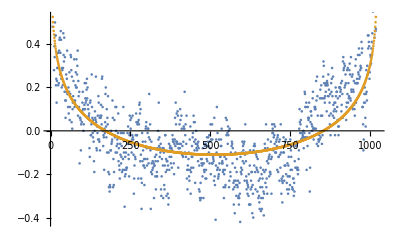

```mathematica
n=1024;
ListPlot[{corr9, Table[-1/(4 Pi)Log[2 - 2 Cos[2 Pi k / n]], {k, 0, n-1}]} ]
```

```mathematica
Moment[Re[fourier9]/n, 1]
Moment[Re[fourier9]/n, 2]
f[1.]/2
```

-0.0160689

0.050134

0.0380693

```mathematica
Moment[Re[mart9], 1]
Moment[Re[mart9], 2]
f[1.]/2
```

-0.0161469

0.0498287

0.0380693

```mathematica
Moment[Re[Dphi9], 1]
Moment[Re[Dphi9], 2]
f[1.]/2
```

-0.0161932

0.0501395

0.0380693